```mathematica
SetDirectory[NotebookDirectory[]];
(* ===ПАРАМЕТРЫ===*)
α=1/137.035999074;
re=2.8179403267*10^-13;
me=0.511;
En0=200.0;
Z=6;           (*Z радиатора*)
Zconv=74;      (*Z конвертора*)
ρmat=19.30;    (*плотность вольфрама,г/см.b3*)
X0diamond=12.13;  (*радиационная длина радиатора (алмаз),см*)
X0conv=0.3504;    (*радиационная длина конвертора (вольфрам),см*)
AW=183.84;     (*атомный вес W*)
NA=6.02214076*10^23;
ρn=N[ρmat*NA/AW];  (*атомная плотность вольфрама,атом/см.b3*)
ΔL=0.001;   (*толщина одного слоя в см*)
NLC=2000;   (*число слоёв*)

(*NIST XCOM:вольфрам W,см.b2/г*)xcomE={0.001,0.0015,0.002,0.003,0.004,0.005,0.006,0.008,0.010,0.015,0.020,0.030,0.040,0.050,0.060,0.080,0.100,0.150,0.200,0.300,0.400,0.500,0.600,0.800,1.0,1.25,1.5,2.0,3.0,4.0,5.0,6.0,8.0,10.0,15.0,20.0,30.0,40.0,50.0,60.0,80.0,100.0};

xcomMu={1.856*10^3,5.765*10^3,1.255*10^4,3.188*10^4,5.685*10^4,3.481*10^4,2.214*10^4,9.883*10^3,4.960*10^3,1.559*10^3,6.504*10^2,1.786*10^2,7.229*10^1,3.691*10^1,2.255*10^1,1.062*10^1,6.573,2.847,1.669,8.318*10^-1,5.835*10^-1,4.900*10^-1,4.467*10^-1,4.320*10^-1,4.681*10^-1,5.143*10^-1,5.553*10^-1,6.347*10^-1,7.948*10^-1,9.448*10^-1,1.084,1.215,1.460,1.683,2.214,2.669,3.440,4.084,4.630,5.105,5.900,6.556};

muInterp=Interpolation[Transpose[{Log[xcomE],Log[xcomMu]}],InterpolationOrder->1];
muC[ω_]:=Exp[muInterp[Log[Max[ω,0.001]]]];

(*NIST ESTAR:позитроны в вольфраме,г/см.b2*)
estarEp={0.01,0.015,0.02,0.03,0.04,0.05,0.06,0.08,0.10,0.15,0.20,0.30,0.40,0.50,0.60,0.80,1.00,1.50,2.00,3.00,4.00,5.00,6.00,8.00,10.0,15.0,20.0,30.0,40.0,50.0,60.0,80.0,100.0,150.0,200.0};

estarRange={0.000292,0.000478,0.000706,0.001283,0.001961,0.002718,0.003530,0.005280,0.007224,0.01296,0.01964,0.03516,0.05237,0.07082,0.09002,0.1313,0.1745,0.2878,0.4030,0.6388,0.8802,1.127,1.377,1.881,2.391,3.681,4.981,7.615,10.28,12.97,15.67,21.10,26.56,40.12,53.70};

estarRangeCm=estarRange/19.30;  (*пробег в см,ρ=19.30 г/см.b3*)
csdaInterp=Interpolation[Transpose[{Log[estarEp],Log[estarRangeCm]}],InterpolationOrder->1];
csdaRange[Ep_]:=Exp[csdaInterp[Log[Max[Ep,0.01]]]];
linearMuPos[Ep_]:=1.0/Max[csdaRange[Ep],1.0*10^-6];

(* ===BH СЕЧЕНИЕ===*)
fcC=N[α^2*Zconv^2*Sum[1/(n*(n^2+α^2*Zconv^2)),{n,1,20}]];
ξC=N[Log[1440/Zconv^(2/3)]/(Log[183/Zconv^(1/3)]-fcC)];
FC=N[(8/3)*Log[Zconv]];
δmaxC=N[Exp[(42.24-FC)/8.368]-0.952];

δBH[Eg_,Ep_]:=me^2*Eg/(2*Ep*(Eg-Ep));
Φ1[Eg_,Ep_]:=Module[{d=δBH[Eg,Ep]},If[d>=δmaxC,0.,20.867-3.242*(d/δmaxC)+0.625*(d/δmaxC)^2]];
Φ2[Eg_,Ep_]:=Module[{d=δBH[Eg,Ep]},If[d>=δmaxC,0.,20.209-1.930*(d/δmaxC)-0.086*(d/δmaxC)^2]];
εminBH[Eg_]:=Max[me/Eg,1/2-1/2*Sqrt[Max[1-(136/Zconv^(1/3))*4*(me/Eg)/δmaxC,0]]];

dSigmaBH[Eg_,Ep_]:=Module[{em=εminBH[Eg],eps=Ep/Eg},If[Ep<=0.||Ep>=Eg||eps<=em||eps>=(1-em),0.,(1/Eg)*α*re^2*Zconv*(Zconv+ξC)*((eps^2+(1-eps)^2)*(Φ1[Eg,Ep]-FC/2)+(2/3)*eps*(1-eps)*(Φ2[Eg,Ep]-FC/2))]];
NEpPts=300;
EpMin=me+0.05;
EpMax=En0-me;
EpGrid=N@Table[EpMin+(EpMax-EpMin)*(j-1)/(NEpPts-1),{j,1,NEpPts}];
PrecomputeSigmaMatrix[EgVec_]:=Module[{NEg=Length[EgVec]},
N@Table[dSigmaBH[EgVec[[k]],EpGrid[[j]]],{k,1,NEg},{j,1,NEpPts}]];
(* Загрузка файла*)
LoadSpectrumFile[path_]:=Module[{raw,l1,l2,l3,l4},raw=Import[path,"Table"];
l1={raw[[#,1]],raw[[#,2]]+raw[[#,4]]}&/@Range[Length[raw]];
l2={raw[[#,1]],raw[[#,4]]}&/@Range[Length[raw]];
l3={raw[[#,1]],raw[[#,5]]}&/@Range[Length[raw]];
l4={raw[[#,1]],raw[[#,6]]}&/@Range[Length[raw]];
{l1,l2,l3,l4}]
(* ===ОСНОВНАЯ ФУНКЦИЯ===*)
ComputeFile[path_,lrad_]:=Module[{data,EgF,IsumF,IincF,IamoF,dEgF,dNdEgG,dNdEgA,X0rad,lradCm,muVec,muPosVec,attPhVec,attPosVec,SigMat,YpF,YpAF,ni,photonsG,photonsA,dYpG,dYpA,specCumG,specCumA,niMaxG,niMaxA,normAnb,specAllG,specAllA},(*Загрузка*)data=Import[path,"Table"];
EgF=data[[All,1]];
IsumF=data[[All,2]];
IincF=data[[All,4]];
IamoF=data[[All,5]];
dEgF=EgF[[2]]-EgF[[1]];
X0rad=12.13;   (*радиационная длина радиатора—алмаз*)
     lradCm=lrad*100.0;
     normAnb=dEgF*Total[(IamoF[[;;-2]]+IamoF[[2;;]])/2];

dNdEgG=N[(lradCm/X0rad)*(IsumF+IincF)/normAnb];
     dNdEgA=N[(lradCm/X0rad)*IamoF/normAnb];
muVec=N[muC[#]*ρmat&/@EgF];muPosVec=N[linearMuPos[#]&/@EpGrid];attPhVec=Exp[-muVec*ΔL];attPosVec=Exp[-muPosVec*ΔL];SigMat=PrecomputeSigmaMatrix[EgF];
YpF=Table[0.,{NLC}];
YpAF=Table[0.,{NLC}];
specAllG=Table[Table[0.,{NEpPts}],{NLC}];
     specAllA=Table[Table[0.,{NEpPts}],{NLC}];
photonsG=N@dNdEgG;
photonsA=N@dNdEgA;
specCumG=Table[0.,{NEpPts}];
specCumA=Table[0.,{NEpPts}];
For[ni=1,ni<=NLC,ni++,dYpG=(dEgF*ρn)*(photonsG.SigMat);
dYpA=(dEgF*ρn)*(photonsA.SigMat);
specCumG=specCumG*attPosVec+dYpG;
specCumA=specCumA*attPosVec+dYpA;
photonsG=photonsG*attPhVec;
photonsA=photonsA*attPhVec;
specAllG[[ni]]=specCumG;
specAllA[[ni]]=specCumA;
YpF[[ni]]=Total[(1/2)*(specCumG[[;;-2]]+specCumG[[2;;]])*(EpGrid[[2;;]]-EpGrid[[;;-2]])];
YpAF[[ni]]=Total[(1/2)*(specCumA[[;;-2]]+specCumA[[2;;]])*(EpGrid[[2;;]]-EpGrid[[;;-2]])];];
niMaxG=Ordering[YpF,-1][[1]];
niMaxA=Ordering[YpAF,-1][[1]];
<|"Yp"->YpF,"YpA"->YpAF,"spec"->specAllG,"specA"->specAllA,"niMax"->niMaxG,"niMaxA"->niMaxA|>]
graphY[r_]:=Module[{ptsCry,ptsAmo,niMaxG,niMaxA,specG,specA},ptsCry=Join[{{0,0}},Table[{ni*ΔL,1000*r["Yp"][[ni]]},{ni,1,NLC}]];
ptsAmo=Join[{{0,0}},Table[{ni*ΔL,1000*r["YpA"][[ni]]},{ni,1,NLC}]];
niMaxG=r["niMax"];
niMaxA=r["niMaxA"];
ListPlot[{ptsCry,ptsAmo},Joined->True,AspectRatio->1,Frame->True,FrameStyle->AbsoluteThickness[2],FrameLabel->{" L_c, cm","10^3Y_p, e^+ per e^-","",""},RotateLabel->True,ImageSize->{800,600},LabelStyle->Directive[Black,FontSize->28, FontFamily-> "Times New Roman" ],PlotStyle->{{Thick,ColorData["DarkBands"][0.3]},{Thick,Dashing[Large],ColorData["SouthwestColors"][1]},{Thick,DotDashed,ColorData["LakeColors"][0.2]},{Thick,Dashing[Large],Thick,ColorData["SouthwestColors"][0.2]},{Thick},{Thick,Blue},{Thick,Dashing[Medium],Red},{Thick,Dashing[Medium],Green},{Thick,Black}},Axes->{False,True}, PlotRange->{0,4.5}]];
graphN[r_]:=Module[{ptsCry,ptsAmo,niMaxG,niMaxA,specG,specA,specRatio},ptsCry=Join[{{0,0}},Table[{ni*ΔL,1000*r["Yp"][[ni]]},{ni,1,NLC}]];
ptsAmo=Join[{{0,0}},Table[{ni*ΔL,1000*r["YpA"][[ni]]},{ni,1,NLC}]];
niMaxG=r["niMax"];
niMaxA=r["niMaxA"];
specG=r["spec"][[niMaxG]];
specA=r["specA"][[niMaxA]];
ListLogPlot[{Select[Transpose[{EpGrid,specG}],#[[2]]>0&],Select[Transpose[{EpGrid,specA}],#[[2]]>0&]},Joined->True,AspectRatio->1,Frame->True,FrameStyle->AbsoluteThickness[2],FrameLabel->{" E_p, MeV","dN_p/dE_p","",""},RotateLabel->True,ImageSize->{800,600},LabelStyle->Directive[Black,FontSize->28, FontFamily-> "Times New Roman" ],PlotStyle->{{Thick,ColorData["DarkBands"][0.3]},{Thick,Dashing[Large],ColorData["SouthwestColors"][1]},{Thick,DotDashed,ColorData["LakeColors"][0.2]},{Thick,Dashing[Large],Thick,ColorData["SouthwestColors"][0.2]},{Thick},{Thick,Blue},{Thick,Dashing[Medium],Red},{Thick,Dashing[Medium],Green},{Thick,Black}},Axes->{False,True}]];
graphMeanEp[path_]:=Module[{r,meanG,meanA,ptsG,ptsA,dEp},r=ComputeFile[path,0.001];
dEp=EpGrid[[2]]-EpGrid[[1]];
(*Средняя энергия:integral(Ep*dN/dEp dEp)/integral(dN/dEp dEp)*)meanG=Table[Module[{spec=r["spec"][[ni]],norm},norm=Total[spec]*dEp;
If[norm>1*^-10,Total[spec*EpGrid]*dEp/norm,0]],{ni,1,NLC}];
meanA=Table[Module[{spec=r["specA"][[ni]],norm},norm=Total[spec]*dEp;
If[norm>1*^-10,Total[spec*EpGrid]*dEp/norm,0]],{ni,1,NLC}];
ptsG=Select[Table[{ni*ΔL,meanG[[ni]]},{ni,1,NLC}],#[[2]]>0&];
ptsA=Select[Table[{ni*ΔL,meanA[[ni]]},{ni,1,NLC}],#[[2]]>0&];
ListLinePlot[{ptsG,ptsA},AspectRatio->1,Frame->True,FrameStyle->AbsoluteThickness[2],FrameLabel->{" \!\(\*SubscriptBox[\(L\), \(c\)]\), cm","\!\(\*SubscriptBox[\(⟨E\), \(p\)]\)⟩, MeV","",""},RotateLabel->True,ImageSize->{800,600},LabelStyle->Directive[Black,FontSize->28,FontFamily->"Times New Roman"],PlotStyle->{{Thick,ColorData["DarkBands"][0.3]},{Thick,Dashing[Large],ColorData["SouthwestColors"][1]}},Axes->{False,True}]];


graphPeakEp[path_]:=Module[{r,peakG,peakA,ptsG,ptsA},r=ComputeFile[path,0.001];
(*Пиковая энергия:Ep при максимуме спектра*)peakG=Table[Module[{spec=r["spec"][[ni]],idx},If[Total[spec]>1*^-10,idx=Ordering[spec,-1][[1]];
EpGrid[[idx]],0]],{ni,1,NLC}];
peakA=Table[Module[{spec=r["specA"][[ni]],idx},If[Total[spec]>1*^-10,idx=Ordering[spec,-1][[1]];
EpGrid[[idx]],0]],{ni,1,NLC}];
ptsG=Select[Table[{ni*ΔL,peakG[[ni]]},{ni,1,NLC}],#[[2]]>0&];
ptsA=Select[Table[{ni*ΔL,peakA[[ni]]},{ni,1,NLC}],#[[2]]>0&];
ListLinePlot[{ptsG,ptsA},AspectRatio->1,Frame->True,FrameStyle->AbsoluteThickness[2],FrameLabel->{" \!\(\*SubscriptBox[\(L\), \(c\)]\), cm","\!\(\*SuperscriptBox[\(E\), \(peak\)]\)\!\(\*SubscriptBox[\(\ \), \(p\)]\), MeV","",""},RotateLabel->True,ImageSize->{800,600},LabelStyle->Directive[Black,FontSize->28,FontFamily->"Times New Roman"],PlotStyle->{{Thick,ColorData["DarkBands"][0.3]},{Thick,Dashing[Large],ColorData["SouthwestColors"][1]}},Axes->{False,True}]];
```

```mathematica
(* Без коллимации*)
{list11,list12,list13, list14}=LoadSpectrumFile["skif10.txt"];
{list21,list22,list23, list24}=LoadSpectrumFile["skif20.txt"];
{list31,list32,list33, list34}=LoadSpectrumFile["skif30.txt"];
{list41,list42,list43, list44}=LoadSpectrumFile["skif40.txt"];
{list51,list52,list53, list54}=LoadSpectrumFile["skif50.txt"];
{list61,list62,list63, list64}=LoadSpectrumFile["skif60.txt"];
```

```mathematica
In1=ListLinePlot[{list11,list12,list13},PlotRange->{0, Automatic},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In2 =ListLinePlot[{list21,list22,list23},PlotRange->{0, Automatic},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In3=ListLinePlot[{list31,list32,list33},PlotRange->{0, Automatic},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In4=ListLinePlot[{list41,list42,list43},PlotRange->{0, Automatic},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In5=ListLinePlot[{list51,list52,list53},PlotRange->{0, Automatic},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In6=ListLinePlot[{list61,list62,list63},PlotRange->{0, Automatic},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
GraphicsGrid[{{In1,In2,In3},{In4,In5,In6}},ImageSize->{2000,1200}, Spacings->{10,10},Frame->All, Alignment->{Center,Top}]
```

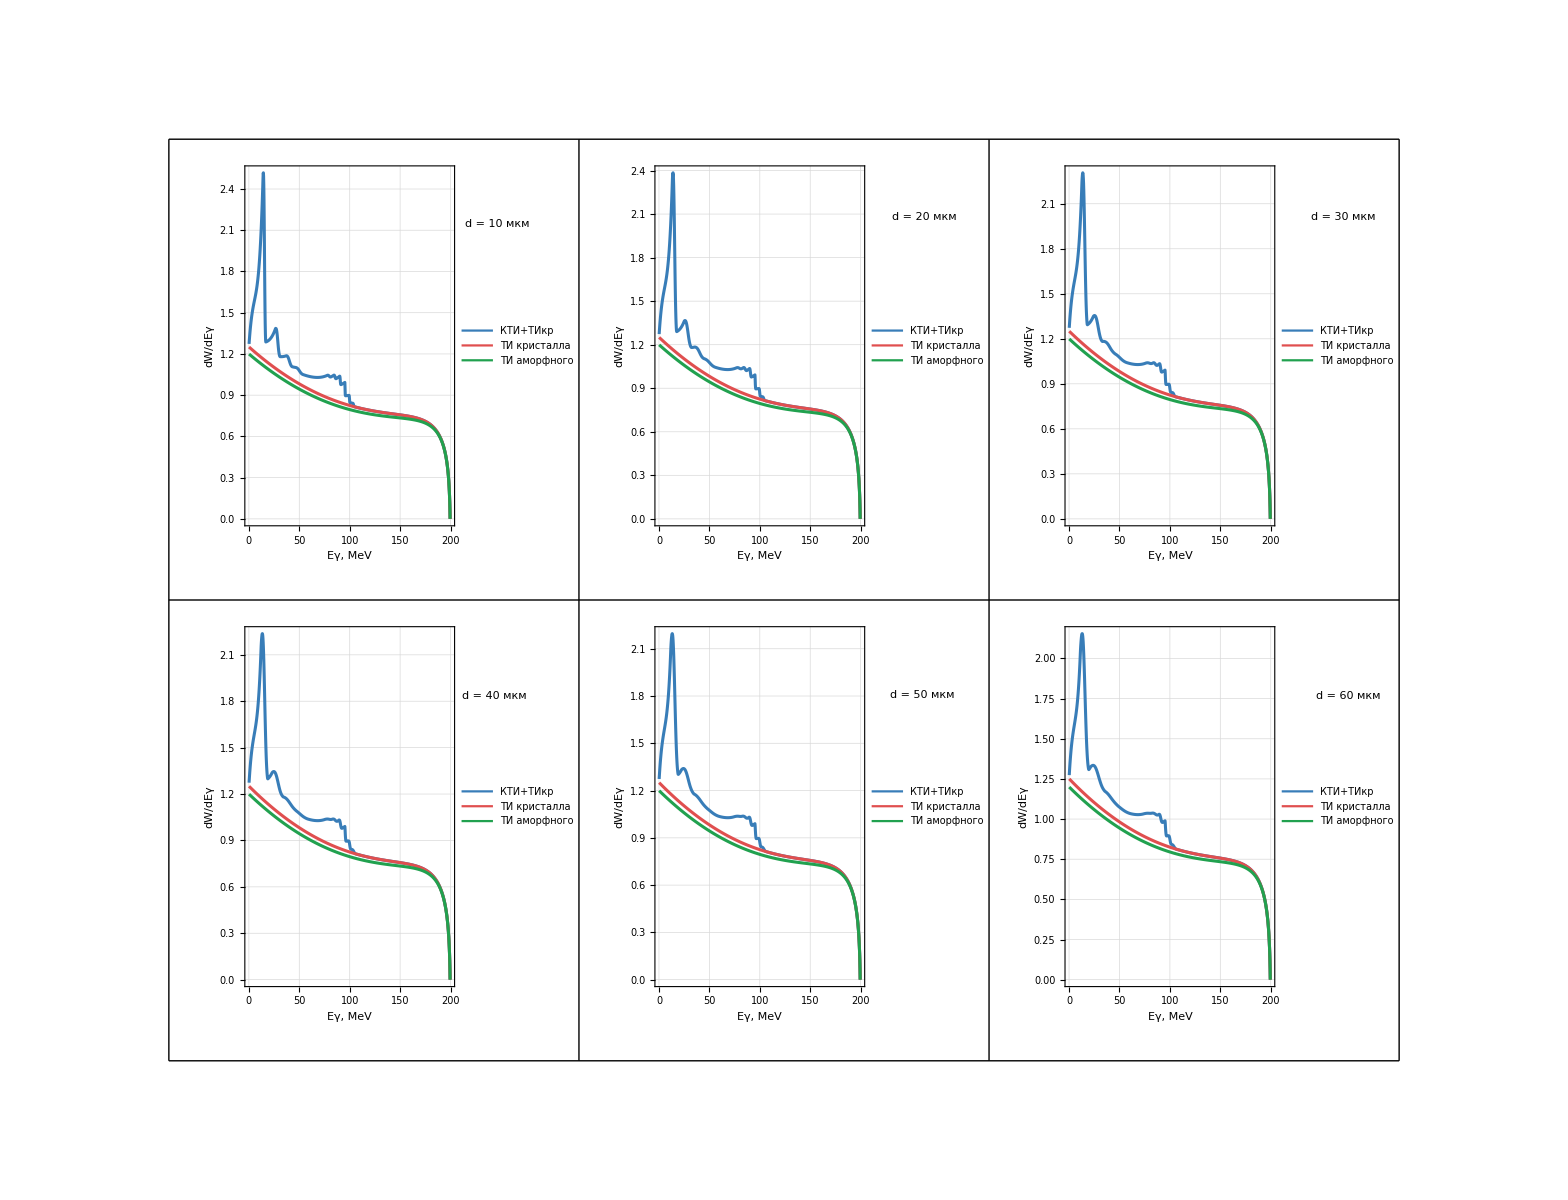

```mathematica
r11=ComputeFile["skif10.txt",10*10^-6];
r12=ComputeFile["skif20.txt",20*10^-6];
r13=ComputeFile["skif30.txt",30*10^-6];
r14=ComputeFile["skif40.txt",40*10^-6];
r15=ComputeFile["skif50.txt",50*10^-6];
r16=ComputeFile["skif60.txt",60*10^-6];
```

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
y11=graphY[r11];
y12=graphY[r12];
y13=graphY[r13];
y14=graphY[r14];
y15=graphY[r15];
y16=graphY[r16];
GraphicsGrid[{{y11,y12,y13},{y14,y15,y16}},ImageSize->{2000,1200}, Spacings->{10,10},Frame->All, Alignment->{Center,Top}]
```

ListPlot::prng: Value of option PlotRange -> {0} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

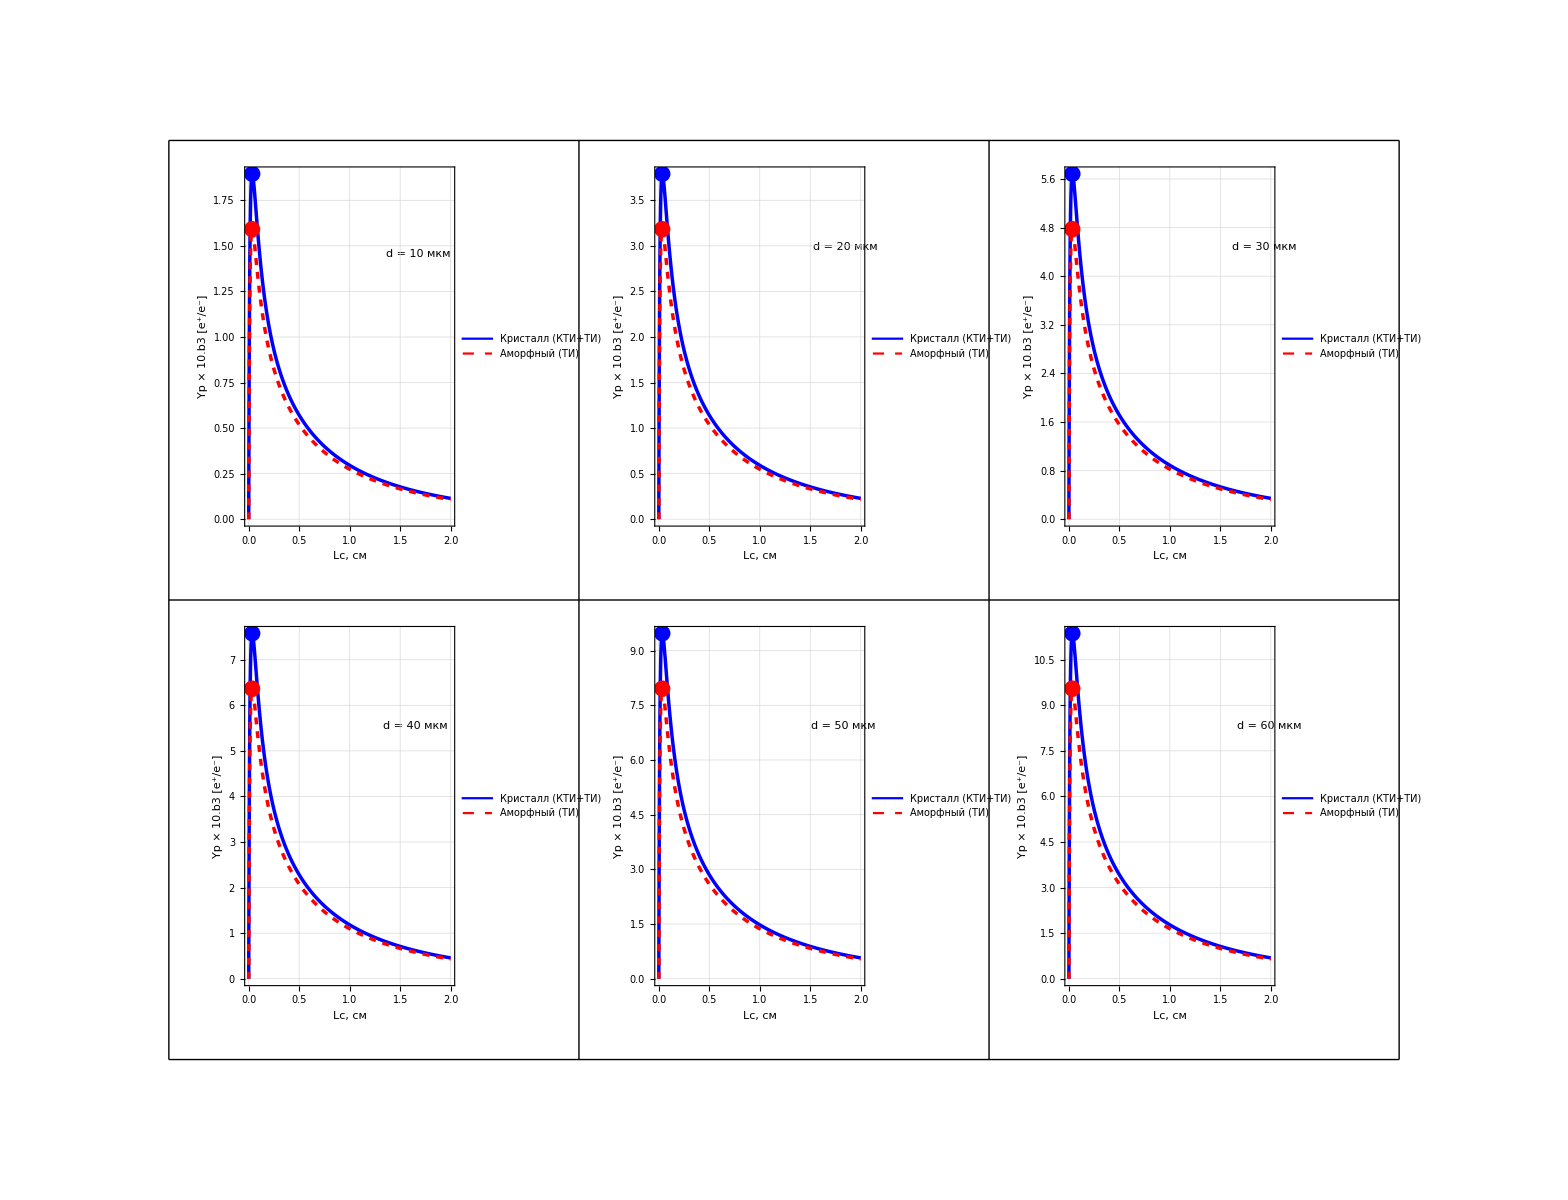

```mathematica
N11=graphN[r11];
N12=graphN[r12];
N13=graphN[r13];
N14=graphN[r14];
N15=graphN[r15];
N16=graphN[r16];
GraphicsGrid[{{N11,N12,N13},{N14,N15,N16}},ImageSize->{2000,1200}, Spacings->{10,10},Frame->All, Alignment->{Center,Top}]
```

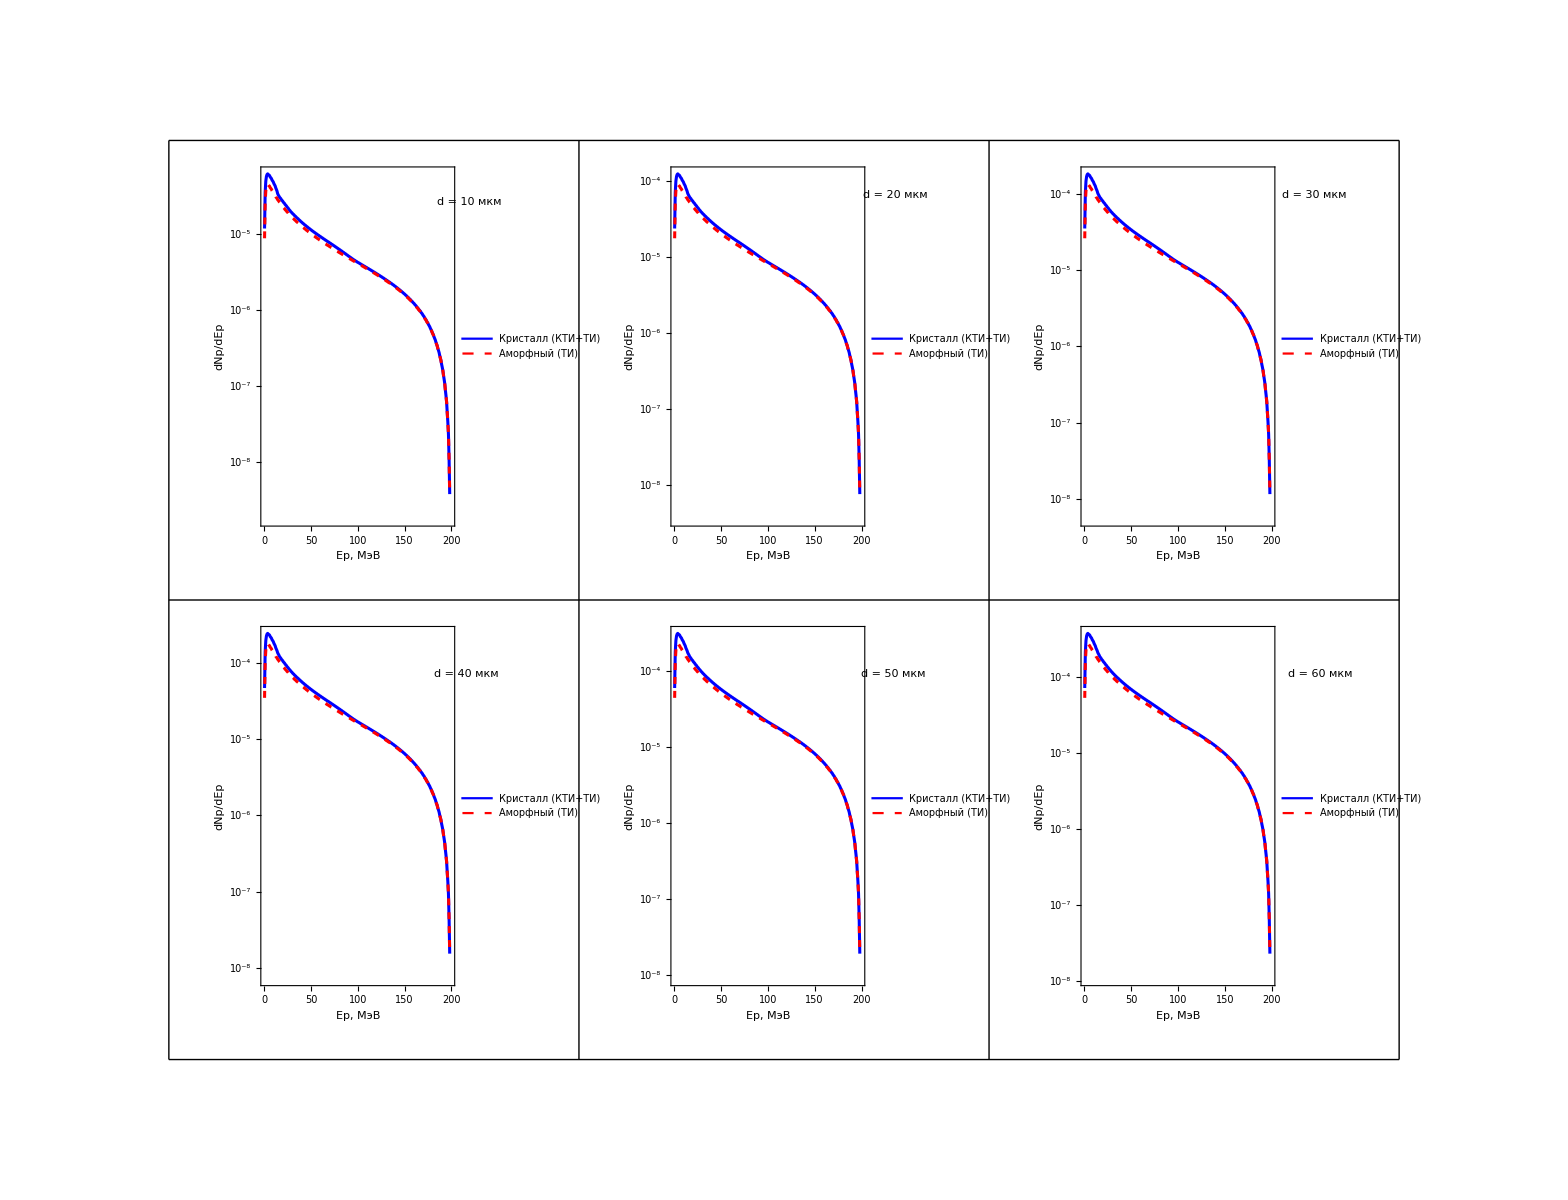

```mathematica
Text[Style["d = 10 мкм", Large]]
```

d = 10 мкм

```mathematica
(* С колимацией, угол коллимации 1/gamma*)
{list11,list12,list13, list14}=LoadSpectrumFile["skif10C.txt"];
{list21,list22,list23, list24}=LoadSpectrumFile["skif20C.txt"];
{list31,list32,list33, list34}=LoadSpectrumFile["skif30C.txt"];
{list41,list42,list43, list44}=LoadSpectrumFile["skif40C.txt"];
{list51,list52,list53, list54}=LoadSpectrumFile["skif50C.txt"];
{list61,list62,list63, list64}=LoadSpectrumFile["skif60C.txt"];
```

```mathematica
In1C=ListLinePlot[{list11,list12,list13},PlotRange->{0, 2},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In2C =ListLinePlot[{list21,list22,list23},PlotRange->{0, 1.8},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In3C=ListLinePlot[{list31,list32,list33},PlotRange->{0, Automatic},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In4C=ListLinePlot[{list41,list42,list43},PlotRange->{0, Automatic},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In5C=ListLinePlot[{list51,list52,list53},PlotRange->{0, Automatic},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In6C=ListLinePlot[{list61,list62,list63},PlotRange->{0, Automatic},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
GraphicsGrid[{{In1C,In2C,In3C},{In4C,In5C,In6C}},ImageSize->{2000,1200}, Spacings->{10,10},Frame->All, Alignment->{Center,Top}]
```

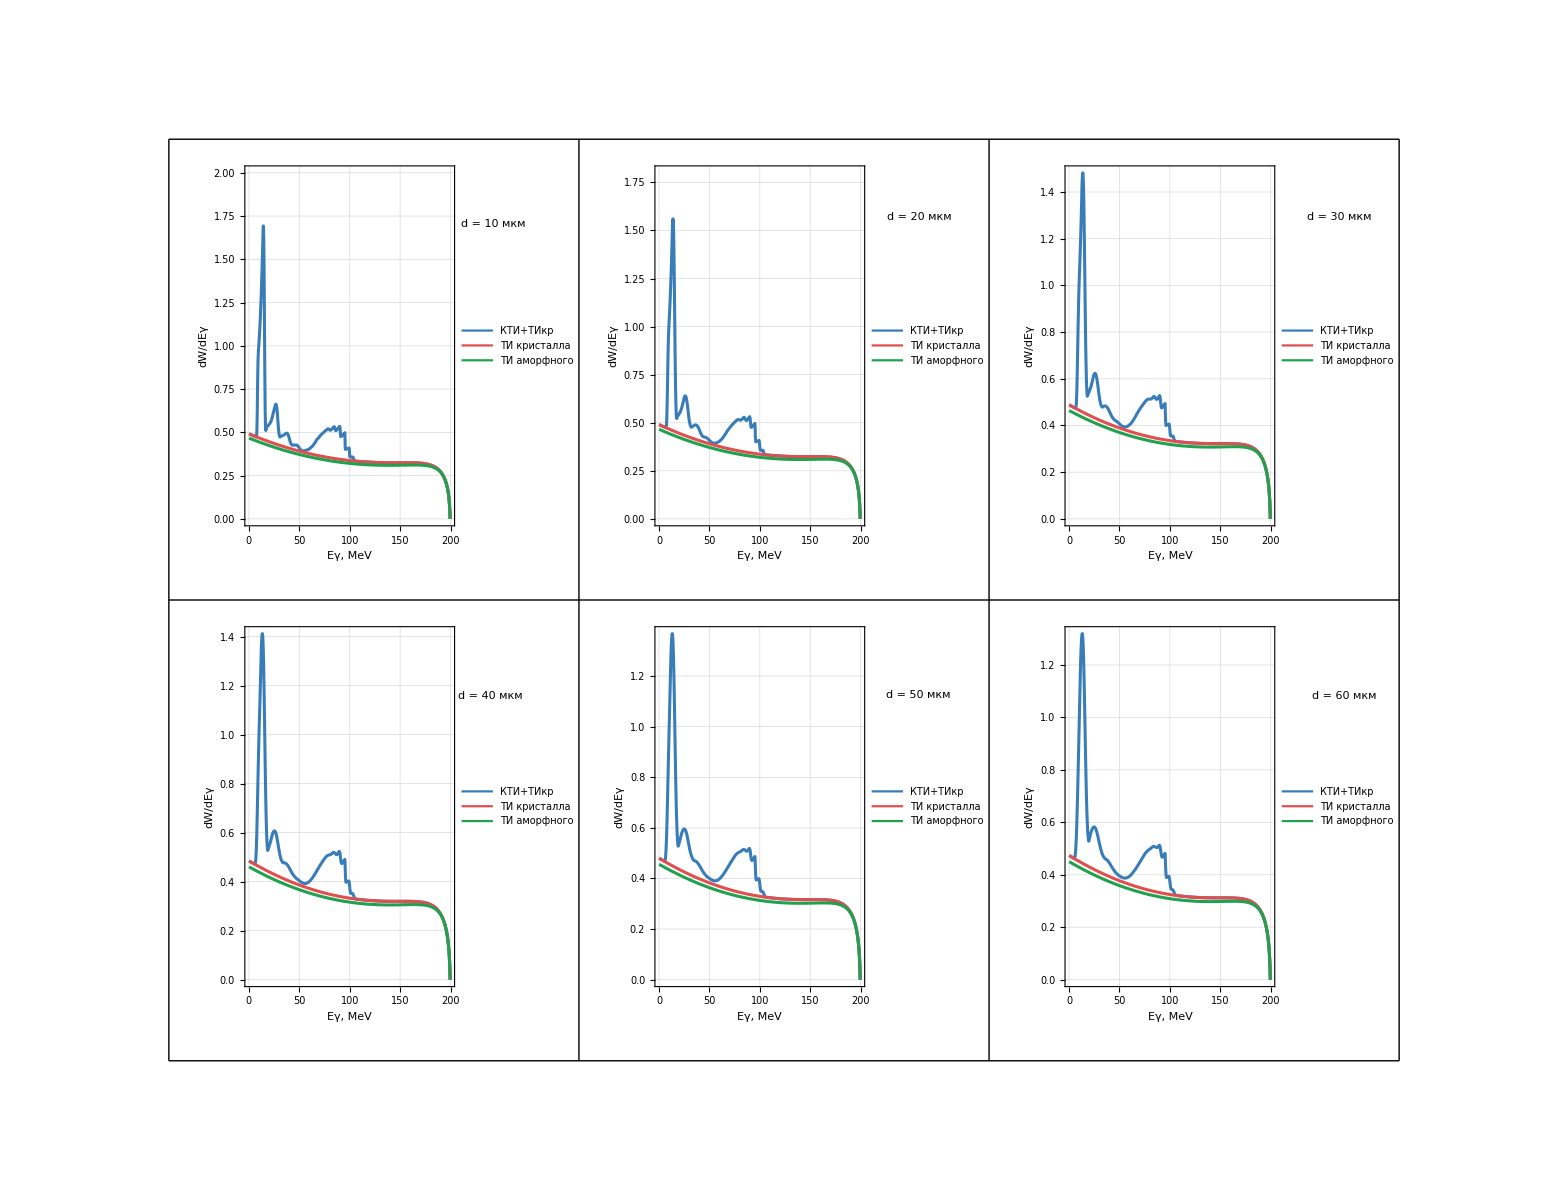

```mathematica
r11=ComputeFile["skif10C.txt",10*10^-6];
r12=ComputeFile["skif20C.txt",20*10^-6];
r13=ComputeFile["skif30C.txt",30*10^-6];
r14=ComputeFile["skif40C.txt",40*10^-6];
r15=ComputeFile["skif50C.txt",50*10^-6];
r16=ComputeFile["skif60C.txt",60*10^-6];
r17=ComputeFile["skif100C.txt",100*10^-6];
```

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
y11=graphY[r11];
y12=graphY[r12];
y13=graphY[r13];
y14=graphY[r14];
y15=graphY[r15];
y16=graphY[r16];
GraphicsGrid[{{y11,y12,y13},{y14,y15,y16}},ImageSize->{2000,1200}, Spacings->{10,10},Frame->All, Alignment->{Center,Top}]
```

ListPlot::prng: Value of option PlotRange -> {0} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

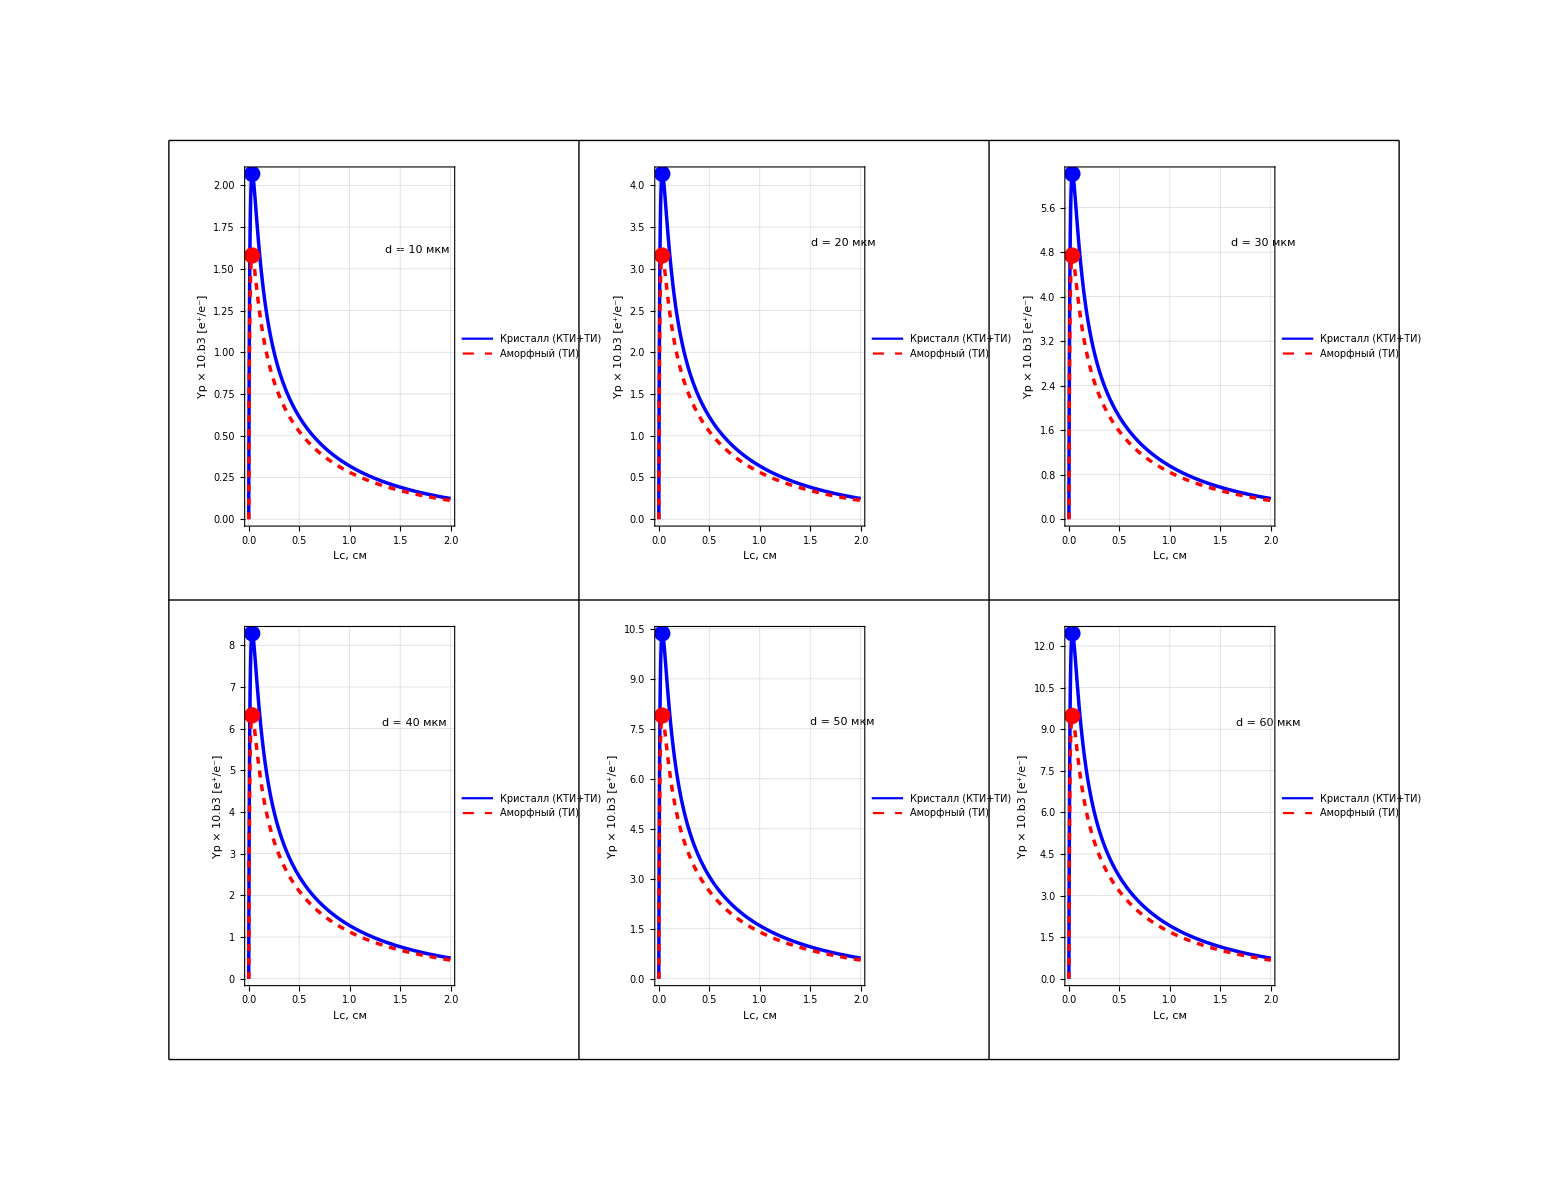

```mathematica
N11=graphN[r11];
N12=graphN[r12];
N13=graphN[r13];
N14=graphN[r14];
N15=graphN[r15];
N16=graphN[r16];
N17=graphN[r17];
Show[N17,N15,N11]
GraphicsGrid[{{N11,N12,N13},{N14,N15,N16}},ImageSize->{2000,1200}, Spacings->{10,10},Frame->All, Alignment->{Center,Top}]
```

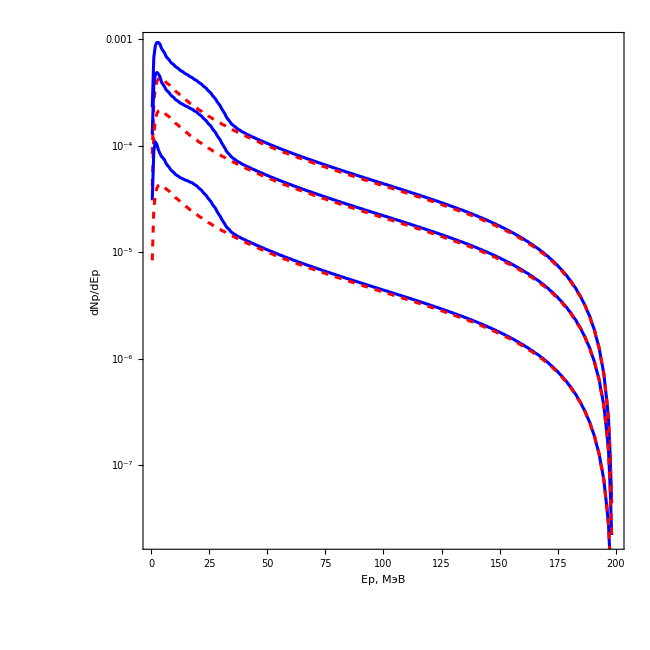

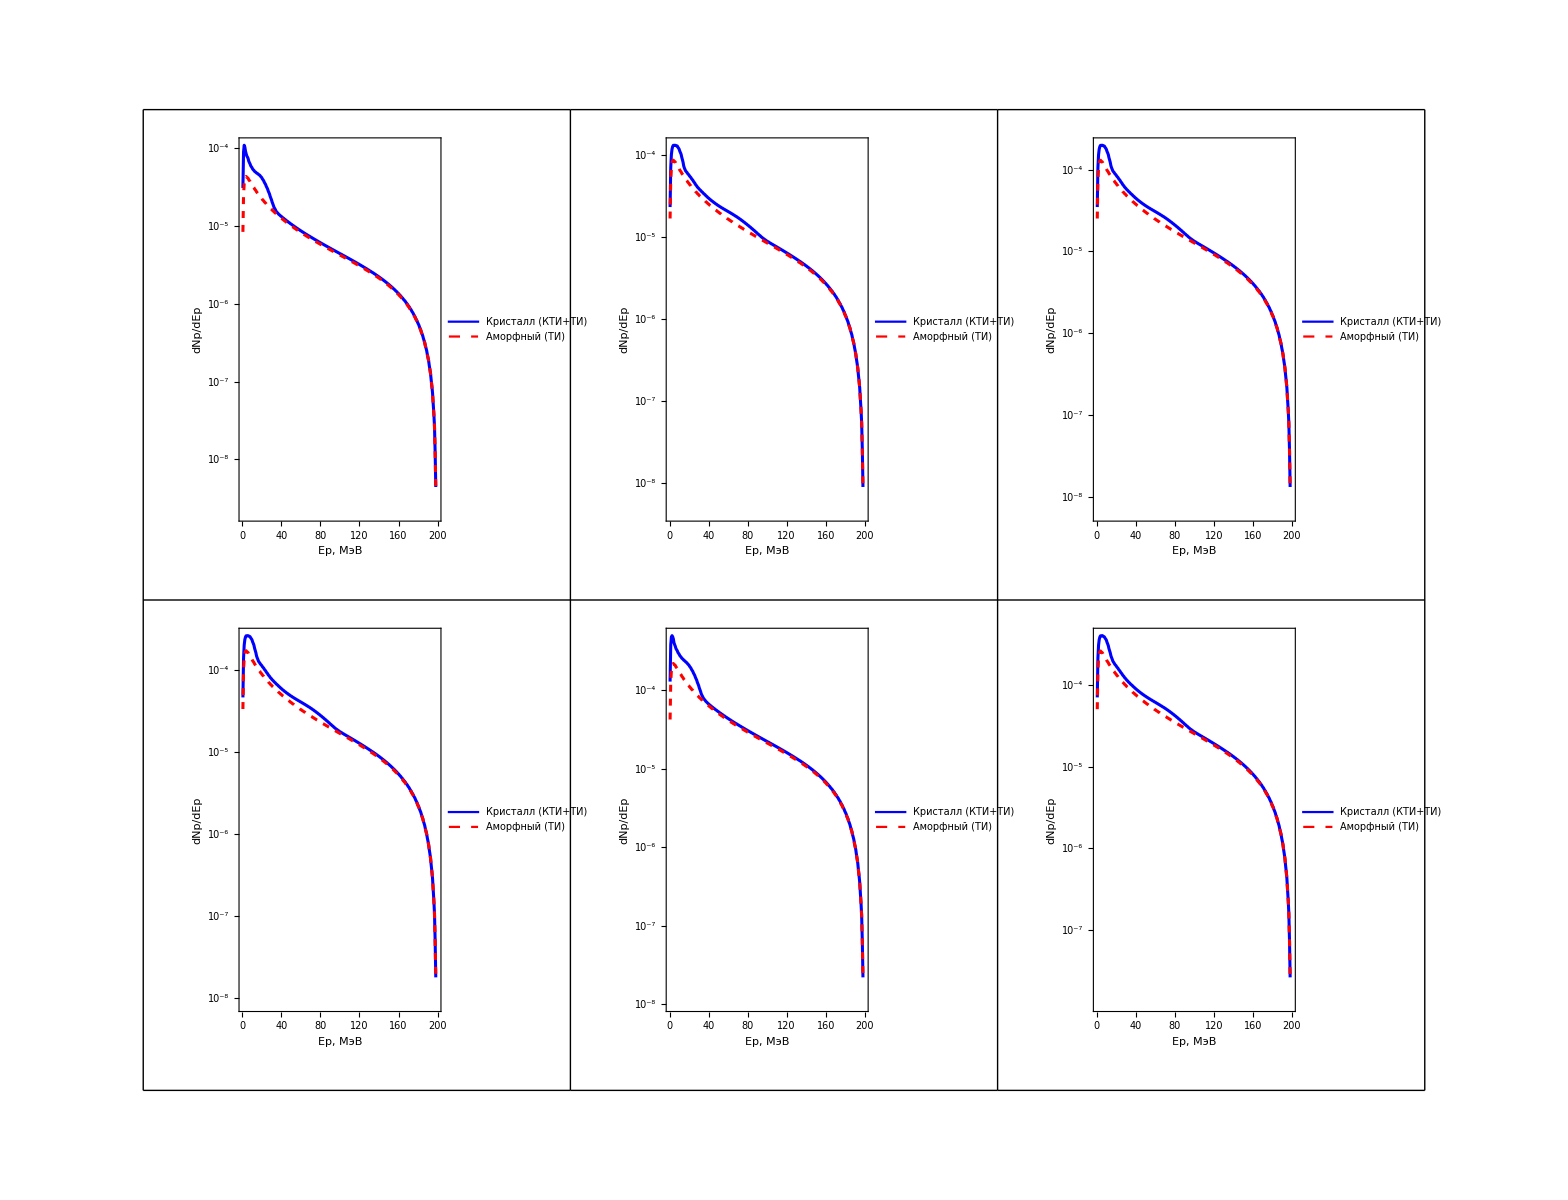

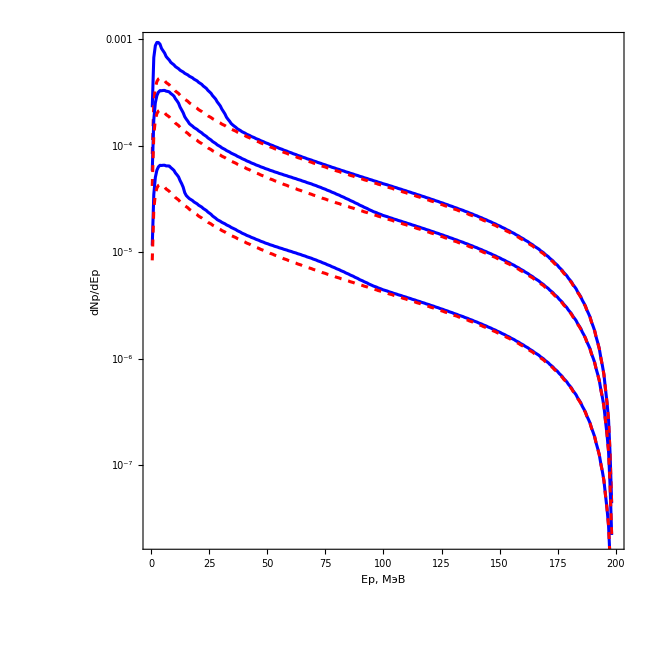

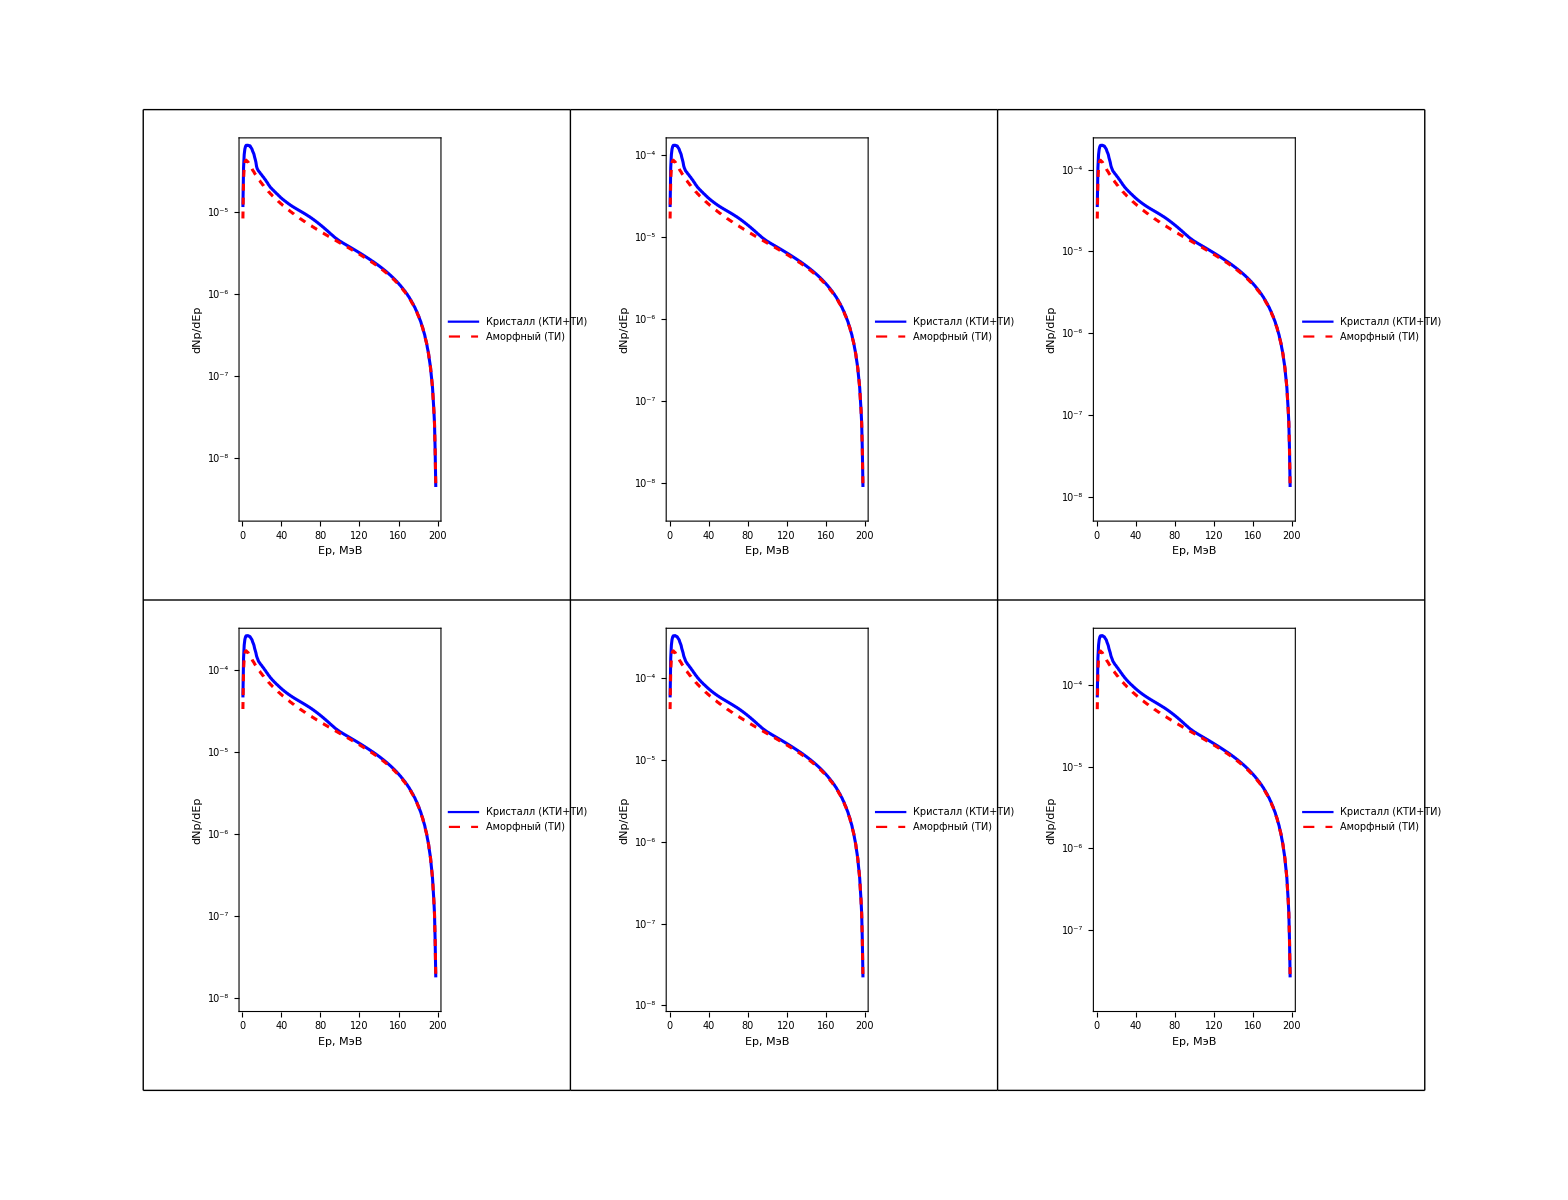

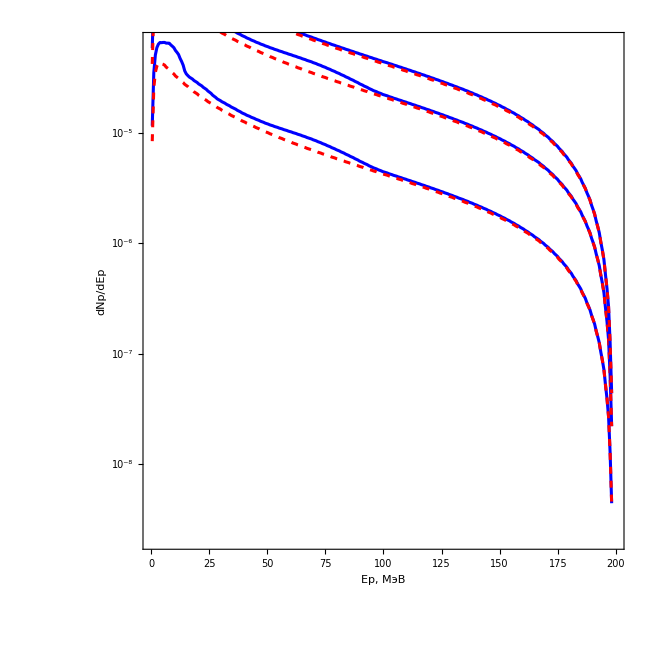

-Graphics-

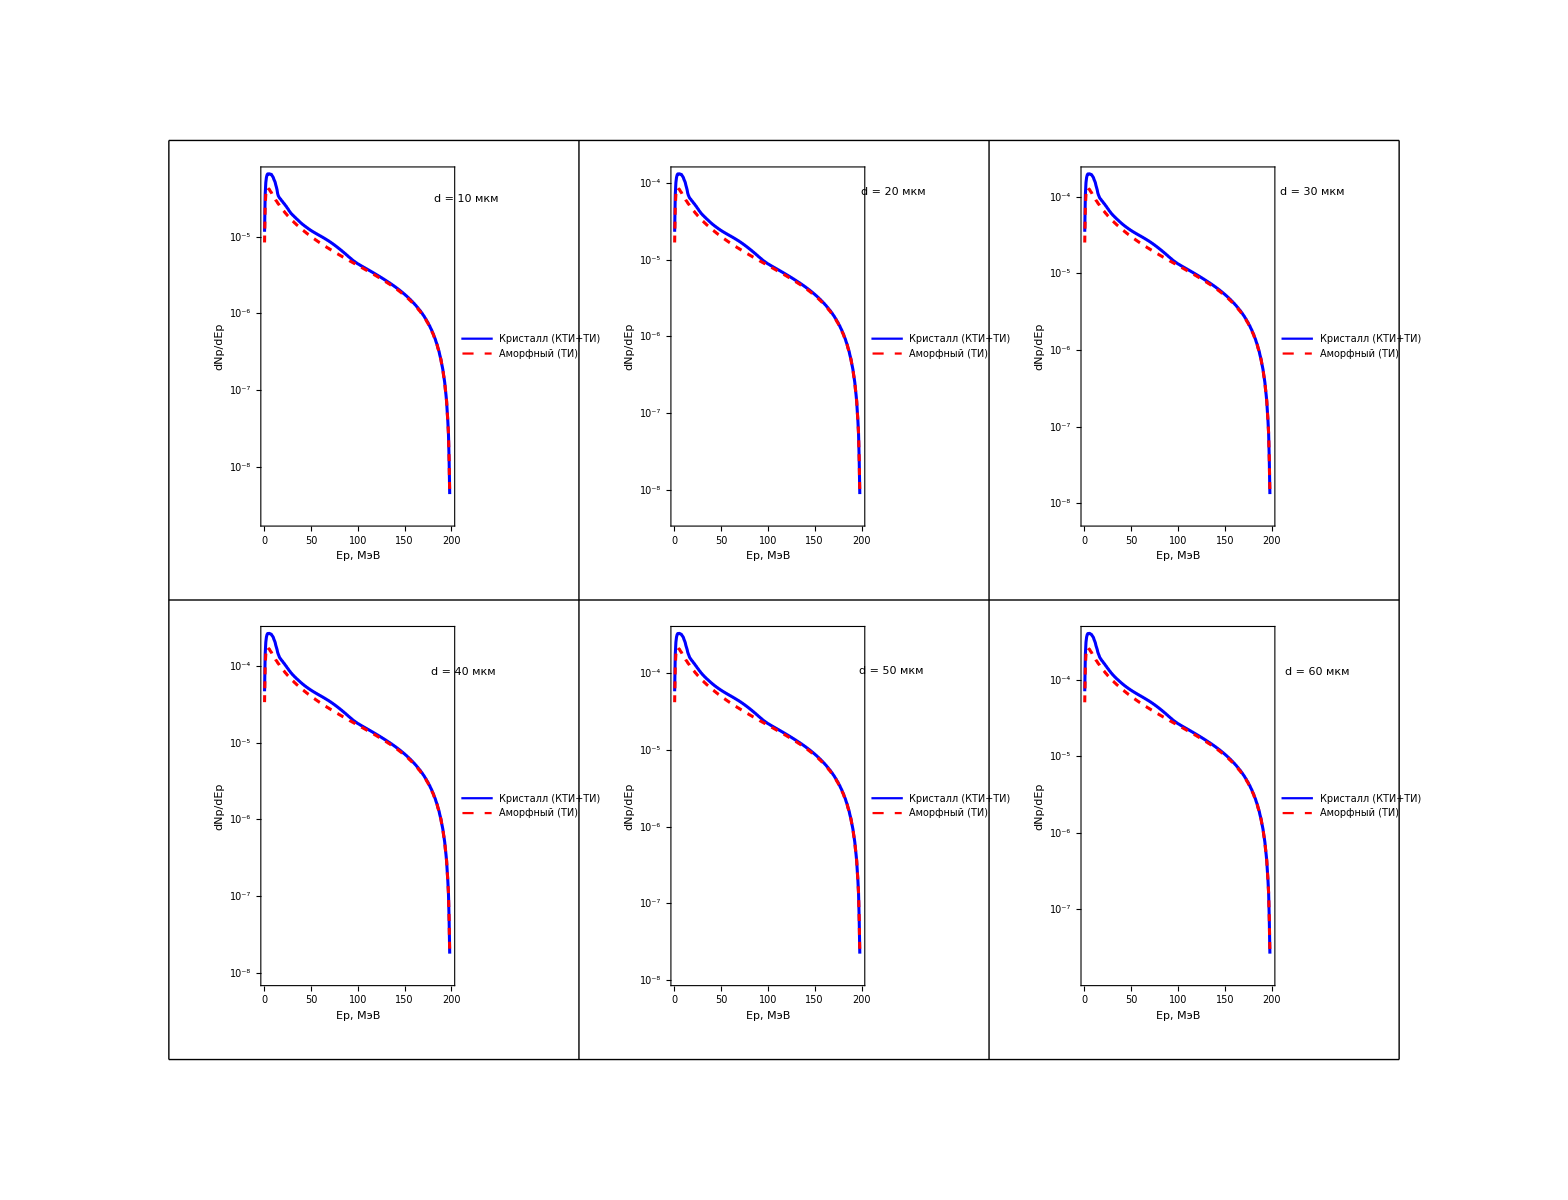

```mathematica
(*С колиматором, толщина радиатора 20мкм, для различных углов колимации*)
{list11,list12,list13, list14}=LoadSpectrumFile["skif20C.txt"];
{list21,list22,list23, list24}=LoadSpectrumFile["skif20C05g.txt"];
{list31,list32,list33, list34}=LoadSpectrumFile["skif20C02g.txt"];
{list41,list42,list43, list44}=LoadSpectrumFile["skif20C01g.txt"];
```

```mathematica
In2C1=ListLinePlot[{list11,list12,list13},PlotRange->{0,2},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In2C05 =ListLinePlot[{list21,list22,list23},PlotRange->{0, 1.3},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In2C02=ListLinePlot[{list31,list32,list33},PlotRange->{0,0.5},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In2C01=ListLinePlot[{list41,list42,list43},PlotRange->{0, 0.1},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
GraphicsGrid[{{In2C1,In2C05},{In2C02,In2C01}},ImageSize->{2000,1200}, Spacings->{10,10},Frame->All, Alignment->{Center,Top}]
```

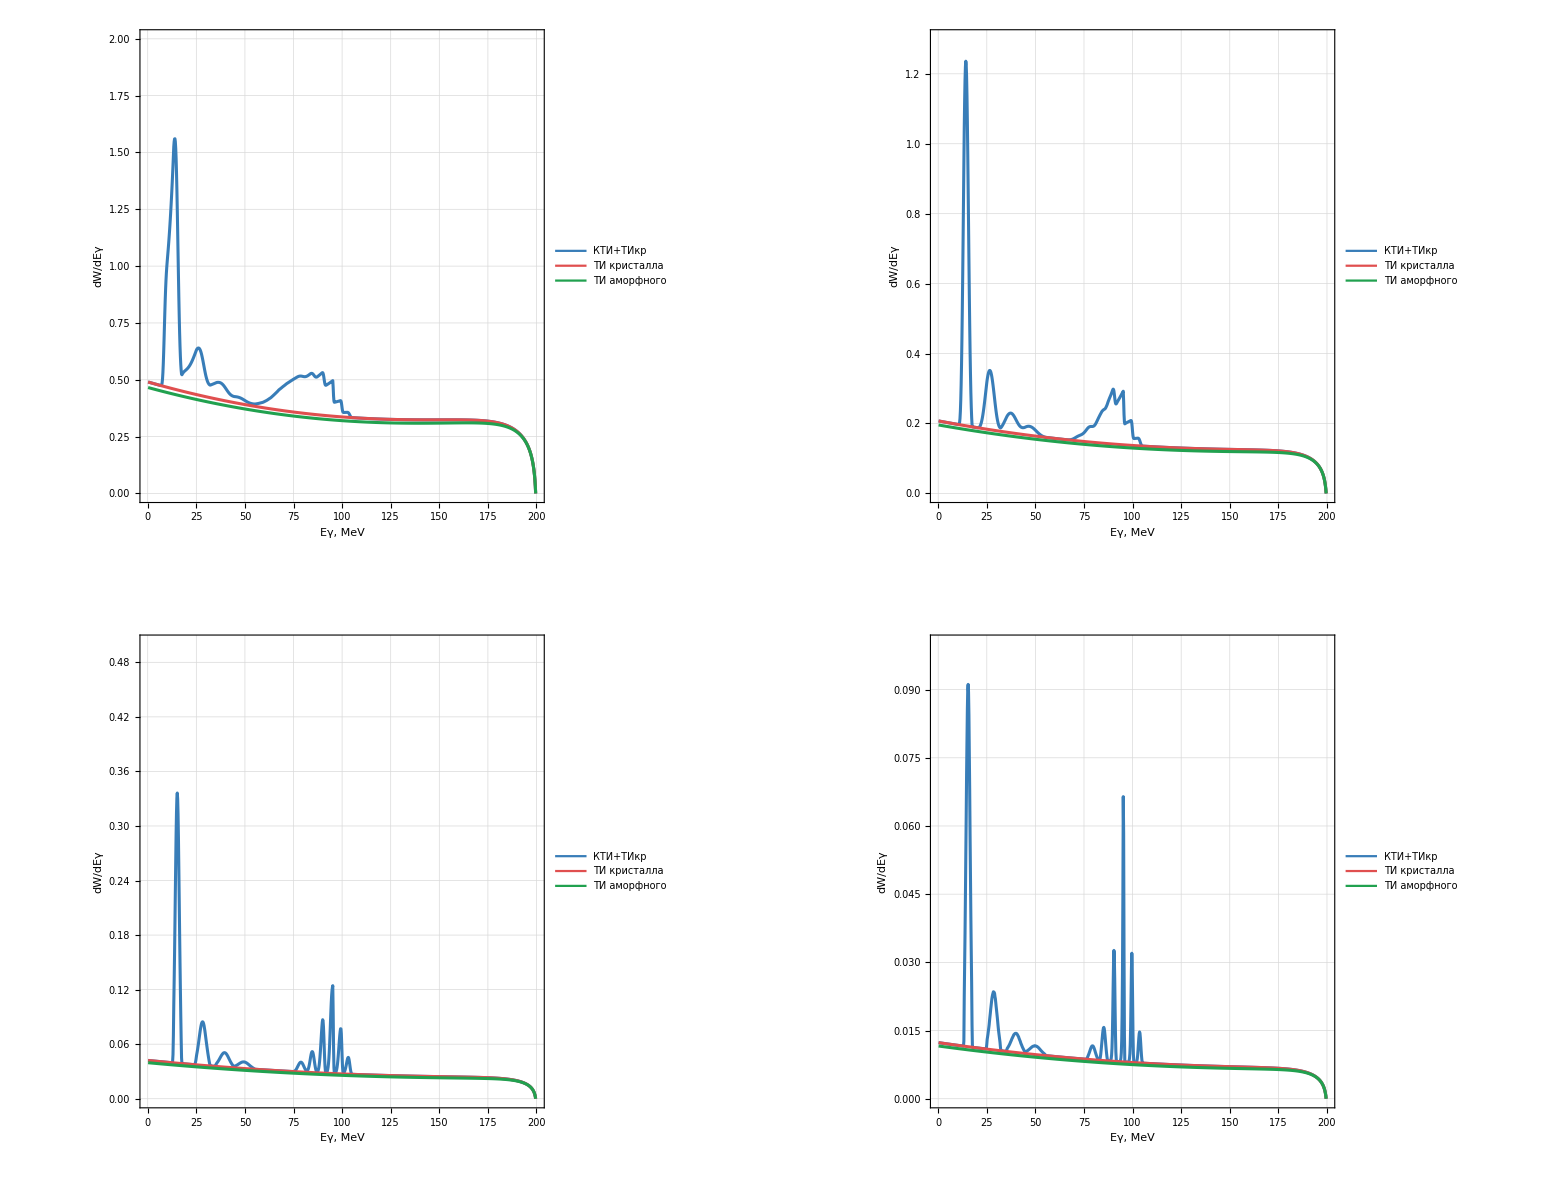

```mathematica
r11=ComputeFile["skif20C.txt",20*10^-6];
r12=ComputeFile["skif20C05g.txt",20*10^-6];
r13=ComputeFile["skif20C02g.txt",20*10^-6];
r14=ComputeFile["skif20C01g.txt",20*10^-6];
```

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
y11=graphY[r11];
y12=graphY[r12];
y13=graphY[r13];
y14=graphY[r14];

GraphicsGrid[{{y11,y12},{y13,y14}},ImageSize->{2000,1200}, Spacings->{10,10},Frame->All, Alignment->{Center,Top}]
```

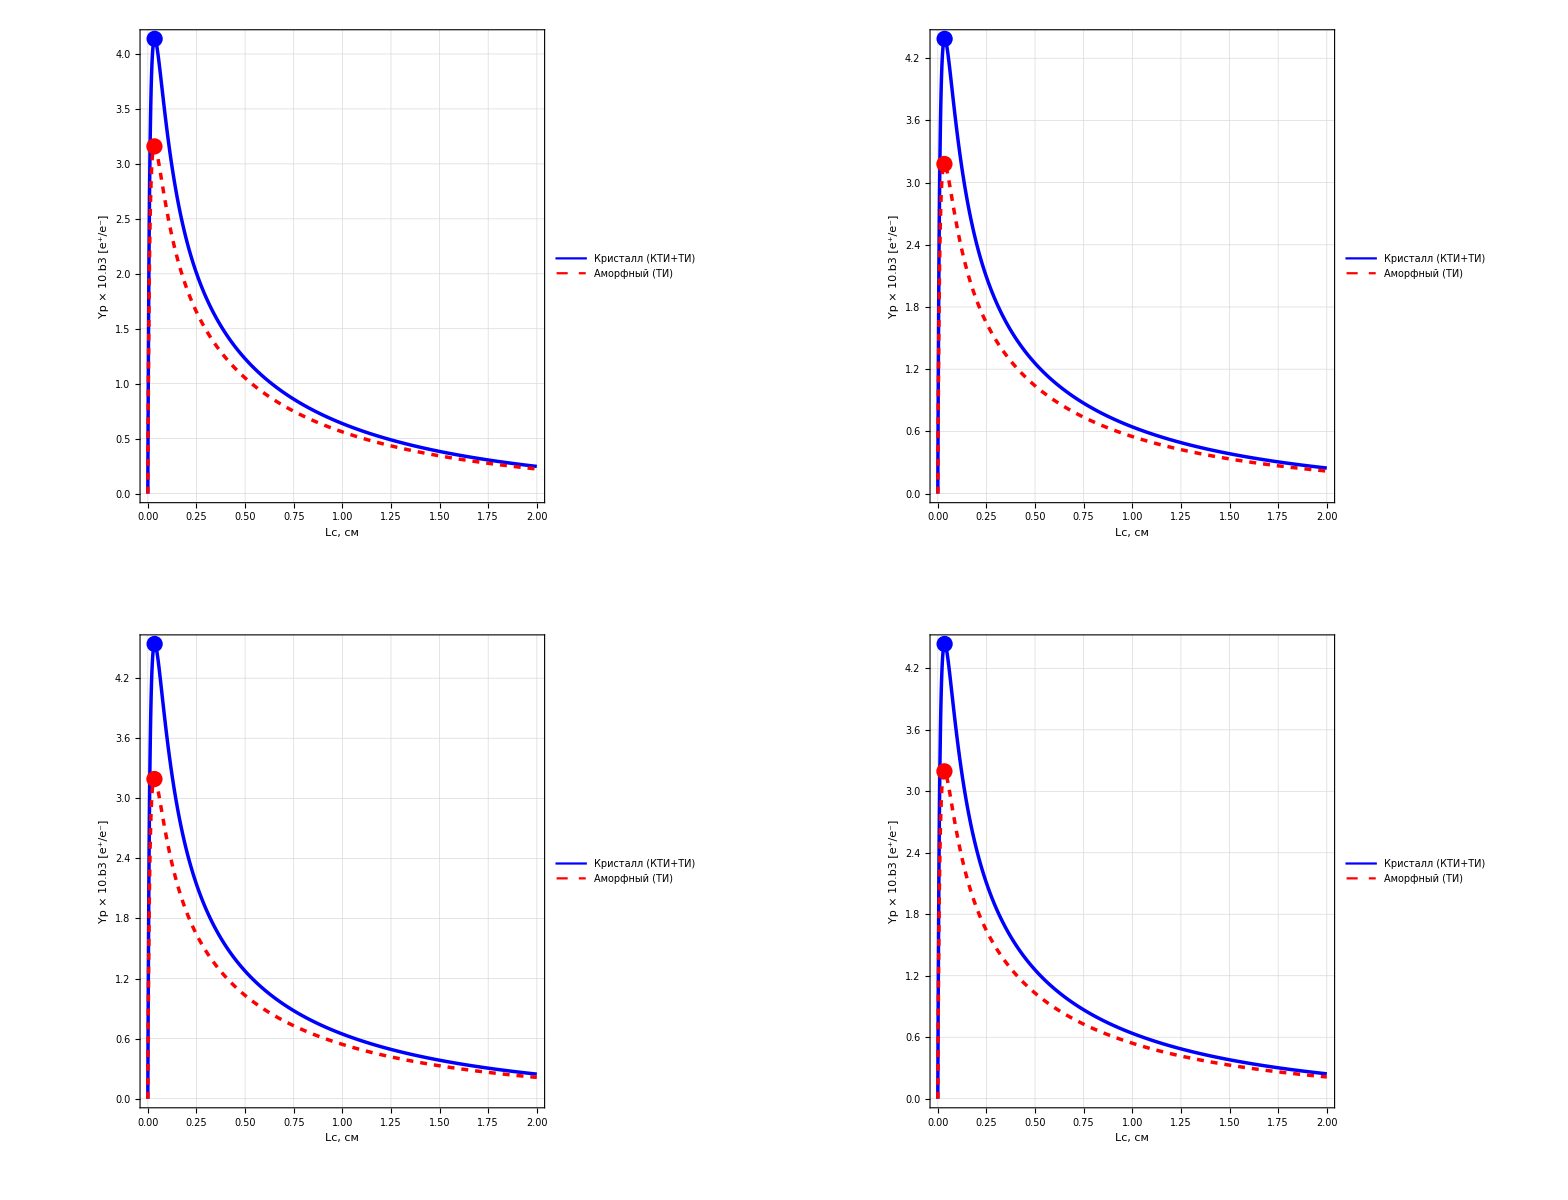

```mathematica
N11=graphN[r11];
N12=graphN[r12];
N13=graphN[r13];
N14=graphN[r14];
GraphicsGrid[{{N11,N12},{N13,N14}},ImageSize->{2000,1200}, Spacings->{10,10},Frame->All, Alignment->{Center,Top}]
```

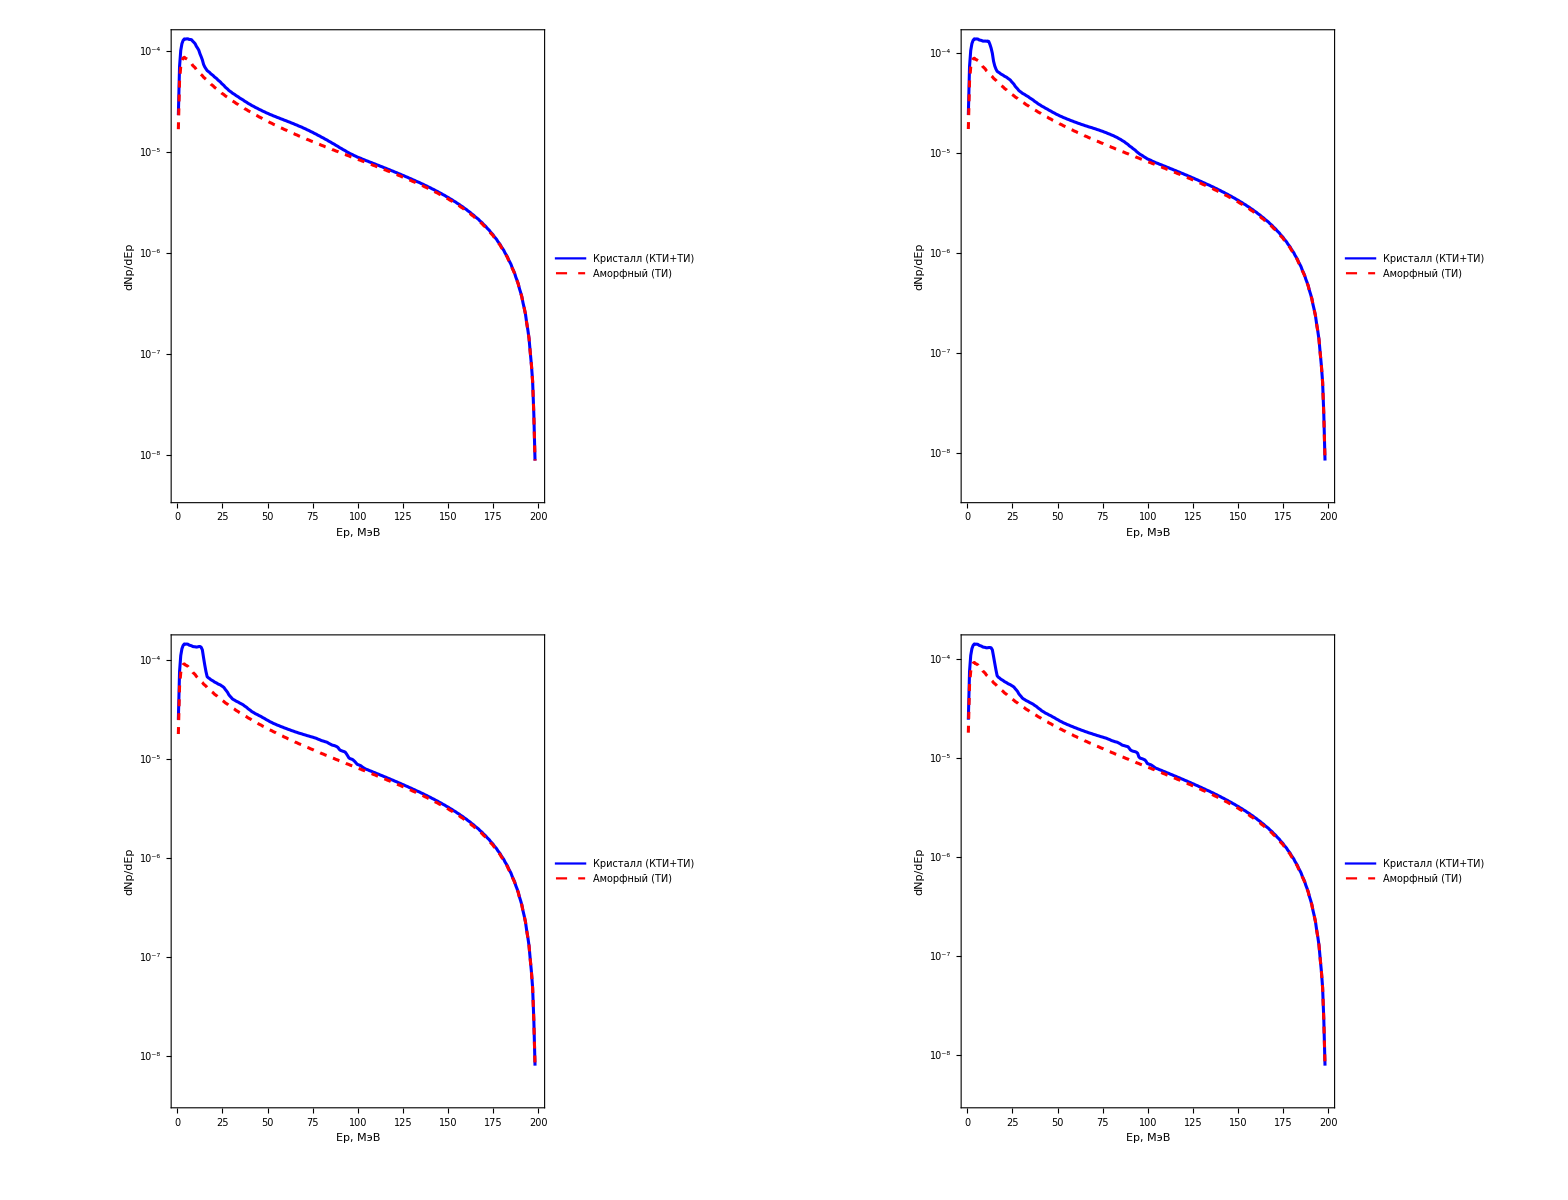

```mathematica
Text[Style[" = 1/10γ", Large]]
```

= 1/10γ

```mathematica
{list11,list12,list13, list14}=LoadSpectrumFile["skif20_5g.txt"];
{list21,list22,list23, list24}=LoadSpectrumFile["skif20_10g.txt"];
{list31,list32,list33, list34}=LoadSpectrumFile["skif20_15g.txt"];
{list41,list42,list43, list44}=LoadSpectrumFile["skif20_20g.txt"];
{list51,list52,list53, list54}=LoadSpectrumFile["skif20_25g.txt"];
{list61,list62,list63, list64}=LoadSpectrumFile["skif20_30g.txt"];
```

```mathematica
In1=ListLinePlot[{list11,list12,list13},PlotRange->{0,5},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In2 =ListLinePlot[{list21,list22,list23},PlotRange->{0, Automatic},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In3=ListLinePlot[{list31,list32,list33},PlotRange->{0, Automatic},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In4=ListLinePlot[{list41,list42,list43},PlotRange->{0, Automatic},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In5=ListLinePlot[{list51,list52,list53},PlotRange->{0, Automatic},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In6=ListLinePlot[{list61,list62,list63},PlotRange->{0, Automatic},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
GraphicsGrid[{{In1,In2,In3},{In4,In5,In6}},ImageSize->{2000,1200}, Spacings->{10,10},Frame->All, Alignment->{Center,Top}]
```

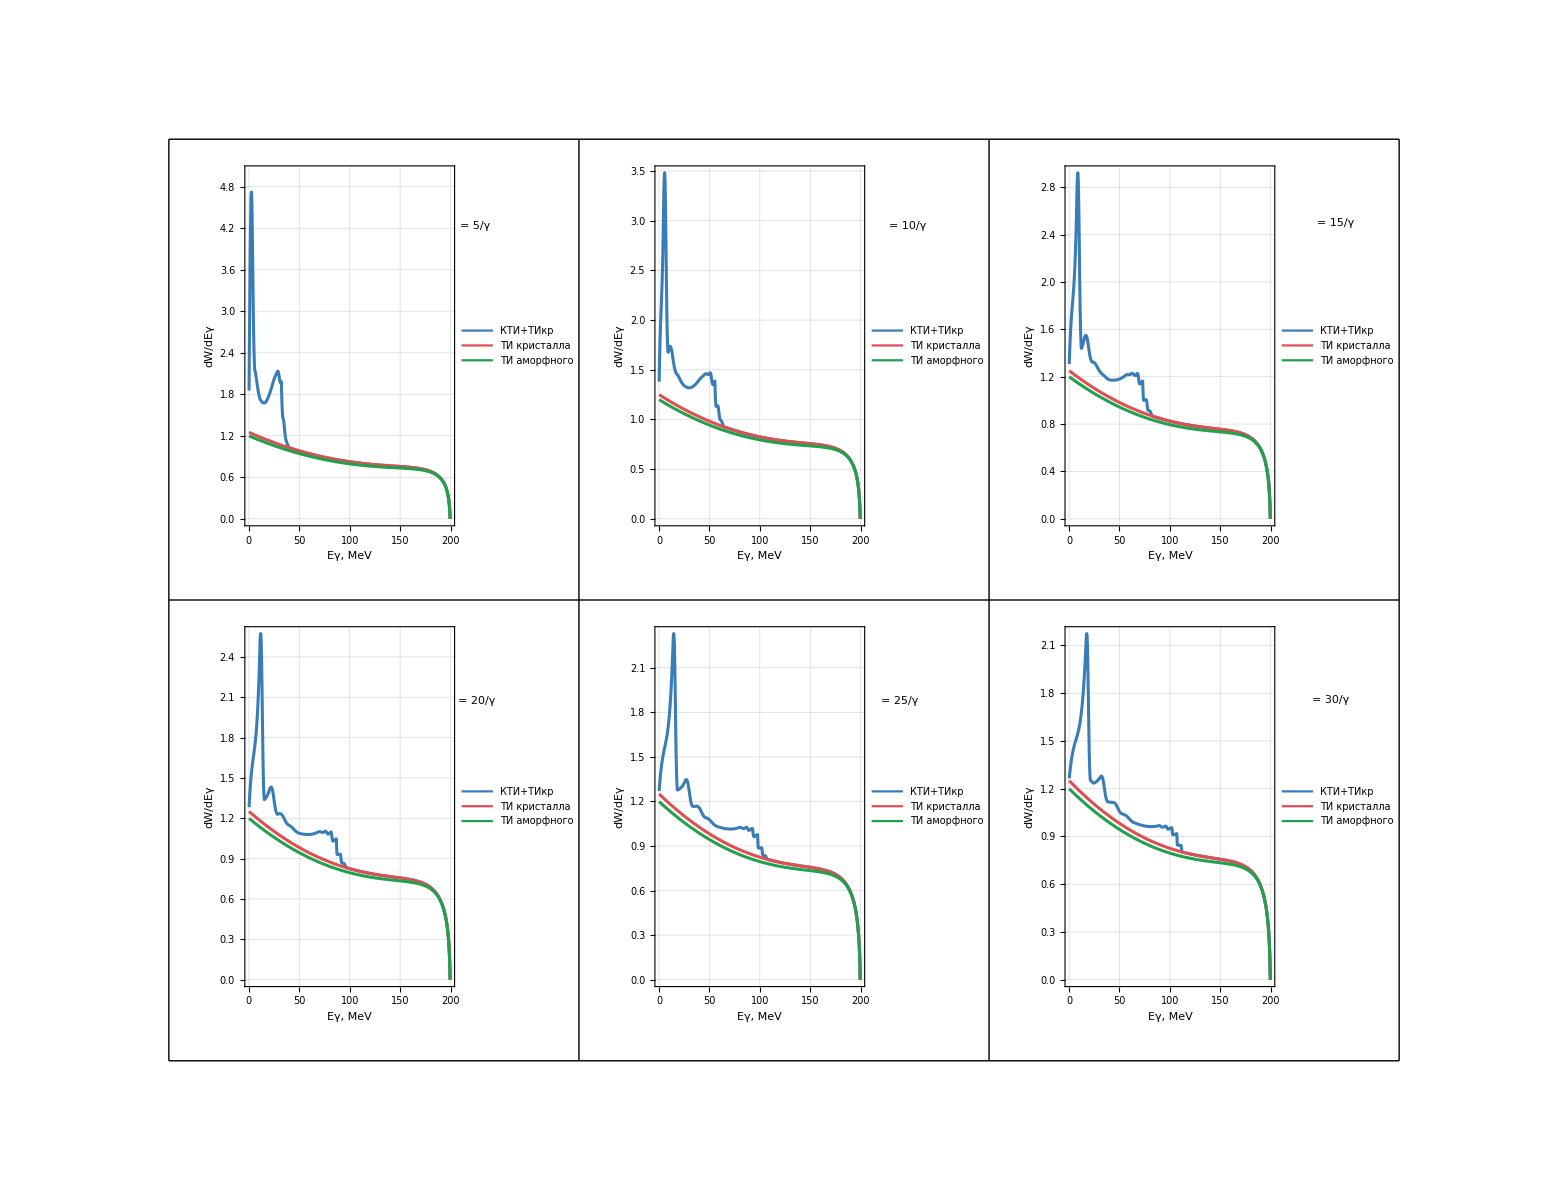

```mathematica
r11=ComputeFile["skif20_5g.txt",20*10^-6];
r12=ComputeFile["skif20_10g.txt",20*10^-6];
r13=ComputeFile["skif20_15g.txt",20*10^-6];
r14=ComputeFile["skif20_20g.txt",20*10^-6];
r15=ComputeFile["skif20_25g.txt",20*10^-6];
r16=ComputeFile["skif20_30g.txt",20*10^-6];
```

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
y11=graphY[r11];
y12=graphY[r12];
y13=graphY[r13];
y14=graphY[r14];
y15=graphY[r15];
y16=graphY[r16];
GraphicsGrid[{{y11,y12,y13},{y14,y15,y16}},ImageSize->{2000,1200}, Spacings->{10,10},Frame->All, Alignment->{Center,Top}]
```

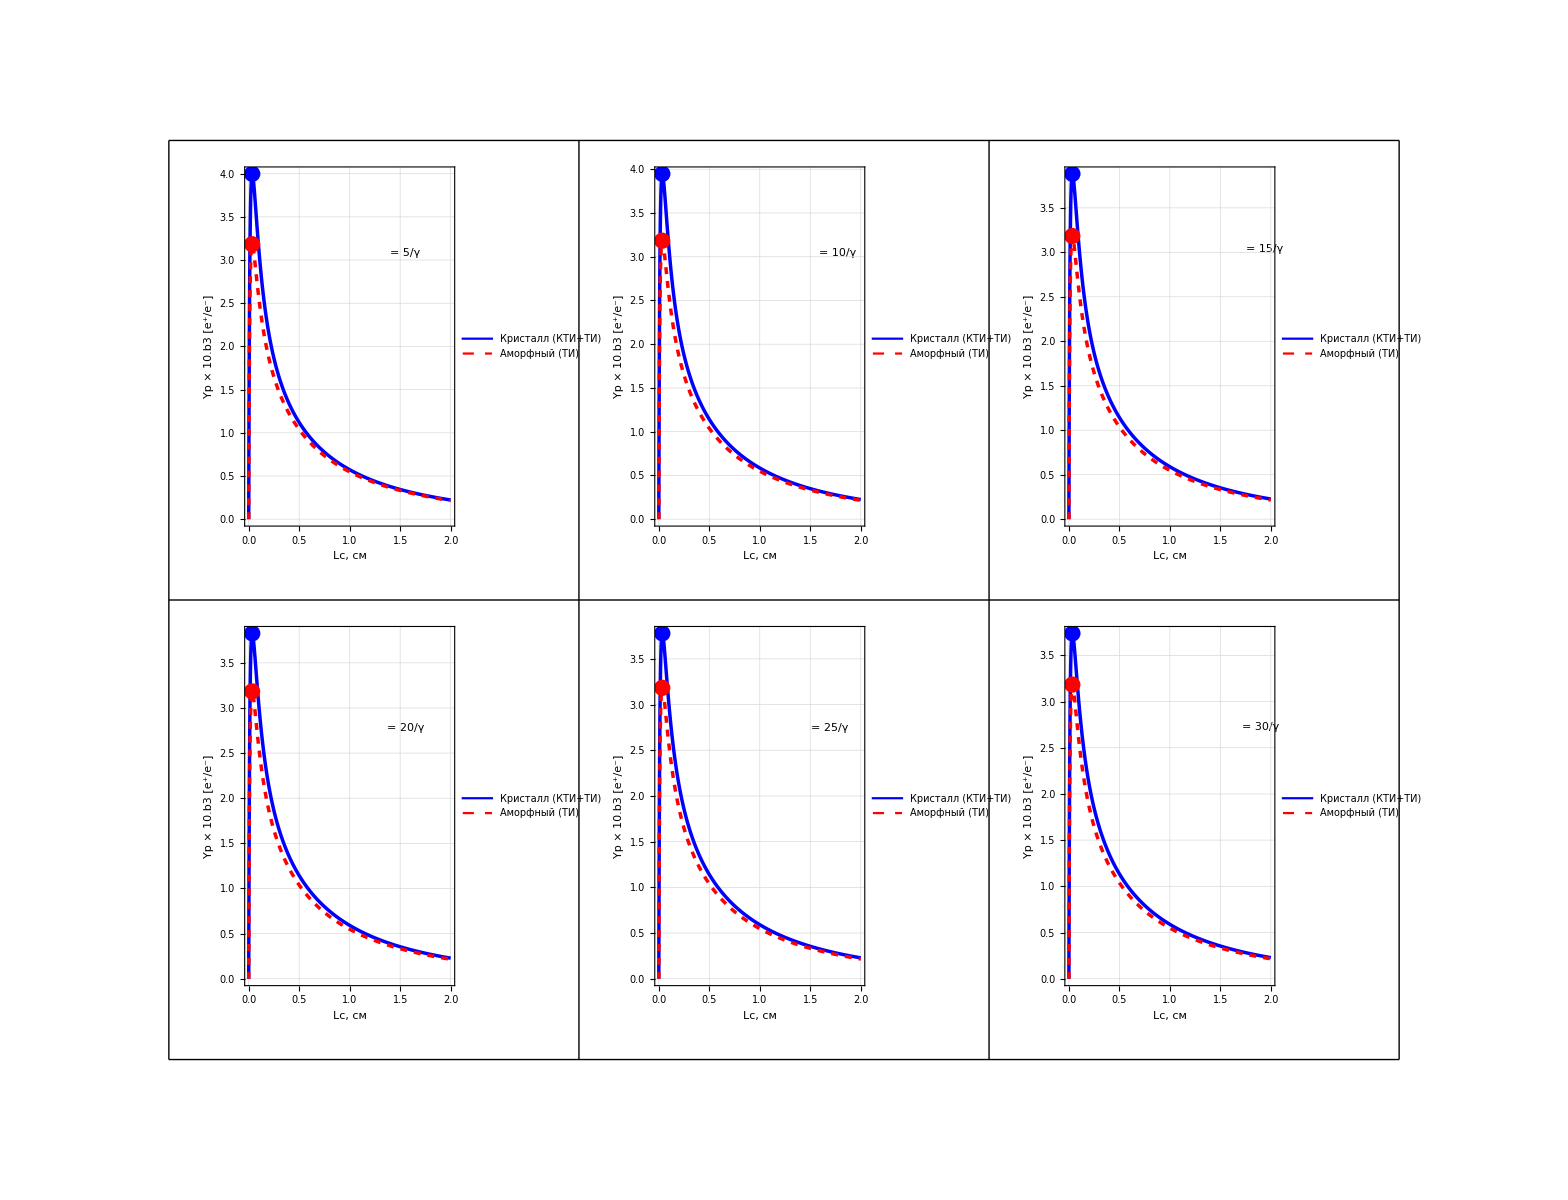

```mathematica
N11=graphN[r11];
N12=graphN[r12];
N13=graphN[r13];
N14=graphN[r14];
N15=graphN[r15];
N16=graphN[r16];
GraphicsGrid[{{N11,N12,N13},{N14,N15,N16}},ImageSize->{2000,1200}, Spacings->{10,10},Frame->All, Alignment->{Center,Top}]
```

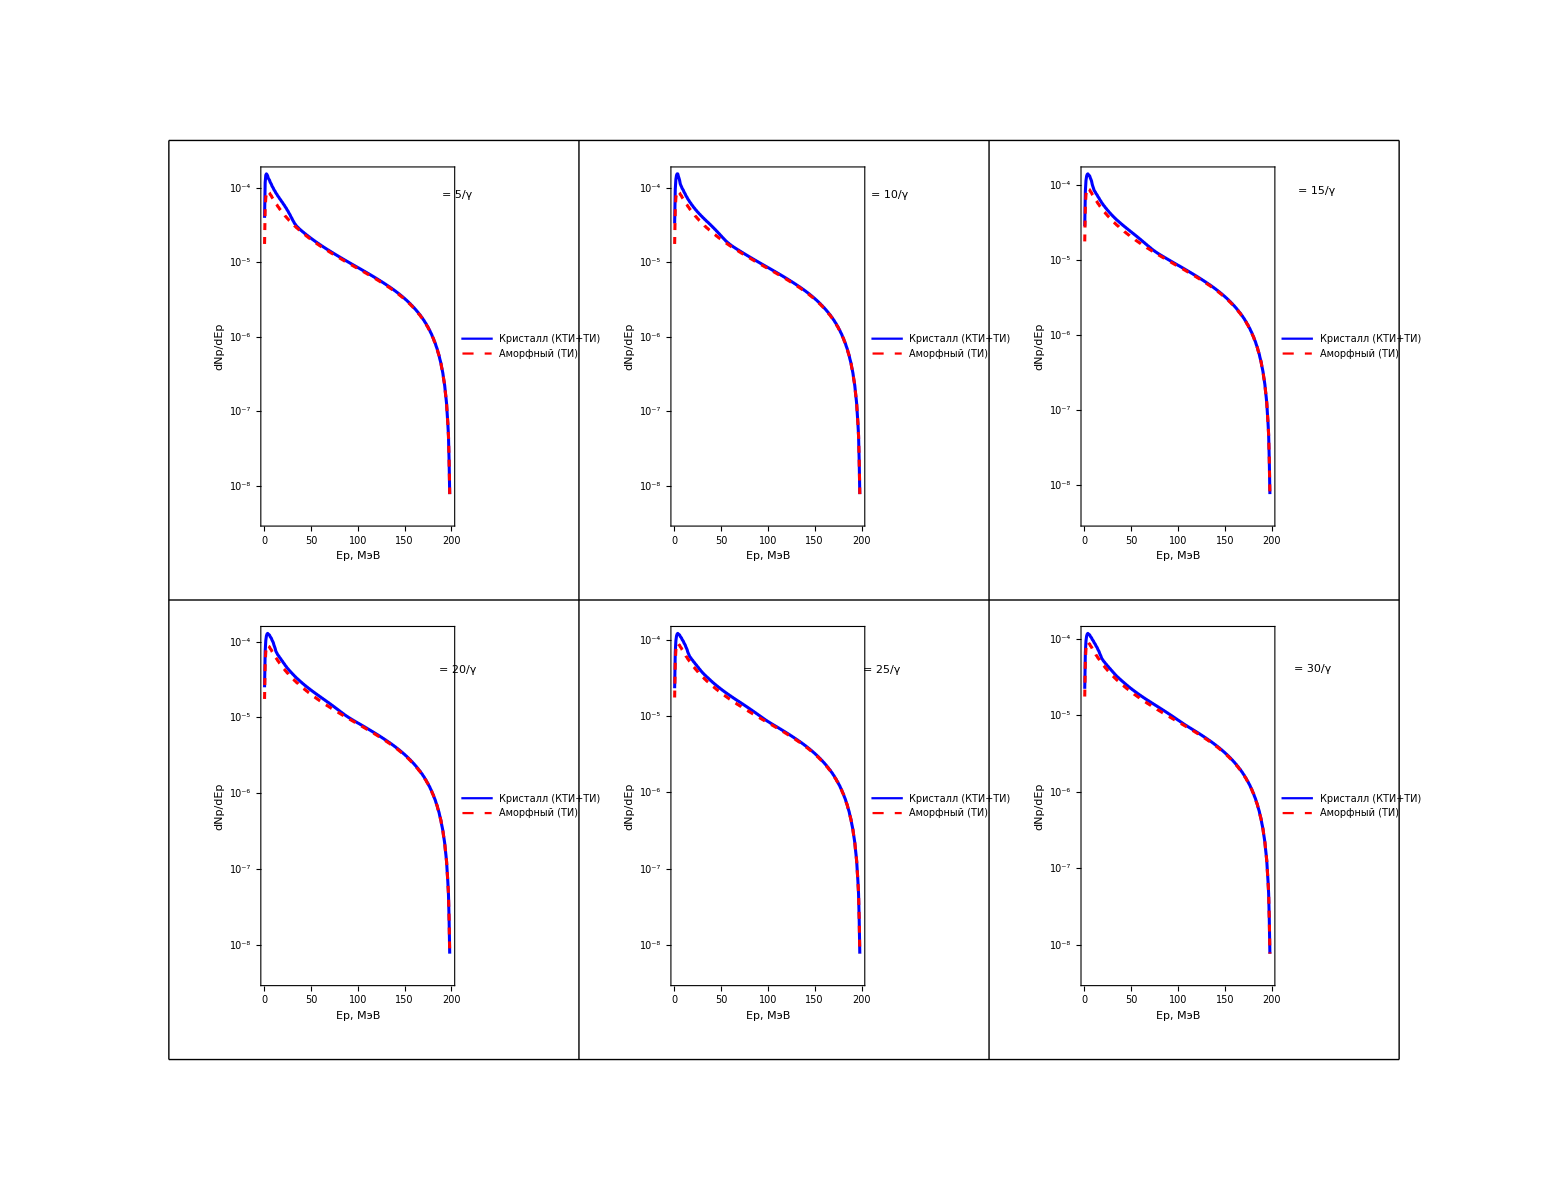

```mathematica
Text[Style[" = 30/γ", Large]]
```

= 30/γ

```mathematica
{list11,list12,list13, list14}=LoadSpectrumFile["skif20_5gC.txt"];
{list21,list22,list23, list24}=LoadSpectrumFile["skif20_10gC.txt"];
{list31,list32,list33, list34}=LoadSpectrumFile["skif20_15gC.txt"];
{list41,list42,list43, list44}=LoadSpectrumFile["skif20_20gC.txt"];
{list51,list52,list53, list54}=LoadSpectrumFile["skif20_25gC.txt"];
{list61,list62,list63, list64}=LoadSpectrumFile["skif20_30gC.txt"];
```

```mathematica
In1=ListLinePlot[{list11,list12,list13},PlotRange->{0, All},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In2 =ListLinePlot[{list21,list22,list23},PlotRange->{0, All},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In3=ListLinePlot[{list31,list32,list33},PlotRange->{0, All},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In4=ListLinePlot[{list41,list42,list43},PlotRange->{0, All},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In5=ListLinePlot[{list51,list52,list53},PlotRange->{0, All},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
In6=ListLinePlot[{list61,list62,list63},PlotRange->{0, All},PlotStyle->{{RGBColor[0.22,0.49,0.72],AbsoluteThickness[2.2]},{RGBColor[0.88,0.31,0.31],AbsoluteThickness[2.2]},{RGBColor[0.13,0.63,0.31],AbsoluteThickness[2.2]},{RGBColor[0.80,0.47,0.13],AbsoluteThickness[2.2]}},PlotLegends->Placed[LineLegend[{RGBColor[0.22,0.49,0.72],RGBColor[0.88,0.31,0.31],RGBColor[0.13,0.63,0.31]},{"КТИ+ТИкр","ТИ кристалла","ТИ аморфного"},LegendMarkers->None,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{Right,Top}],BaseStyle->{FontFamily->"Times New Roman",FontSize->20},Frame->True,FrameLabel->{Style["Eγ, MeV",20],Style["dW/dEγ",20]},RotateLabel->True,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->{600,560},AspectRatio->1];
GraphicsGrid[{{In1,In2,In3},{In4,In5,In6}},ImageSize->{2000,1200}, Spacings->{10,10},Frame->All, Alignment->{Center,Top}]
```

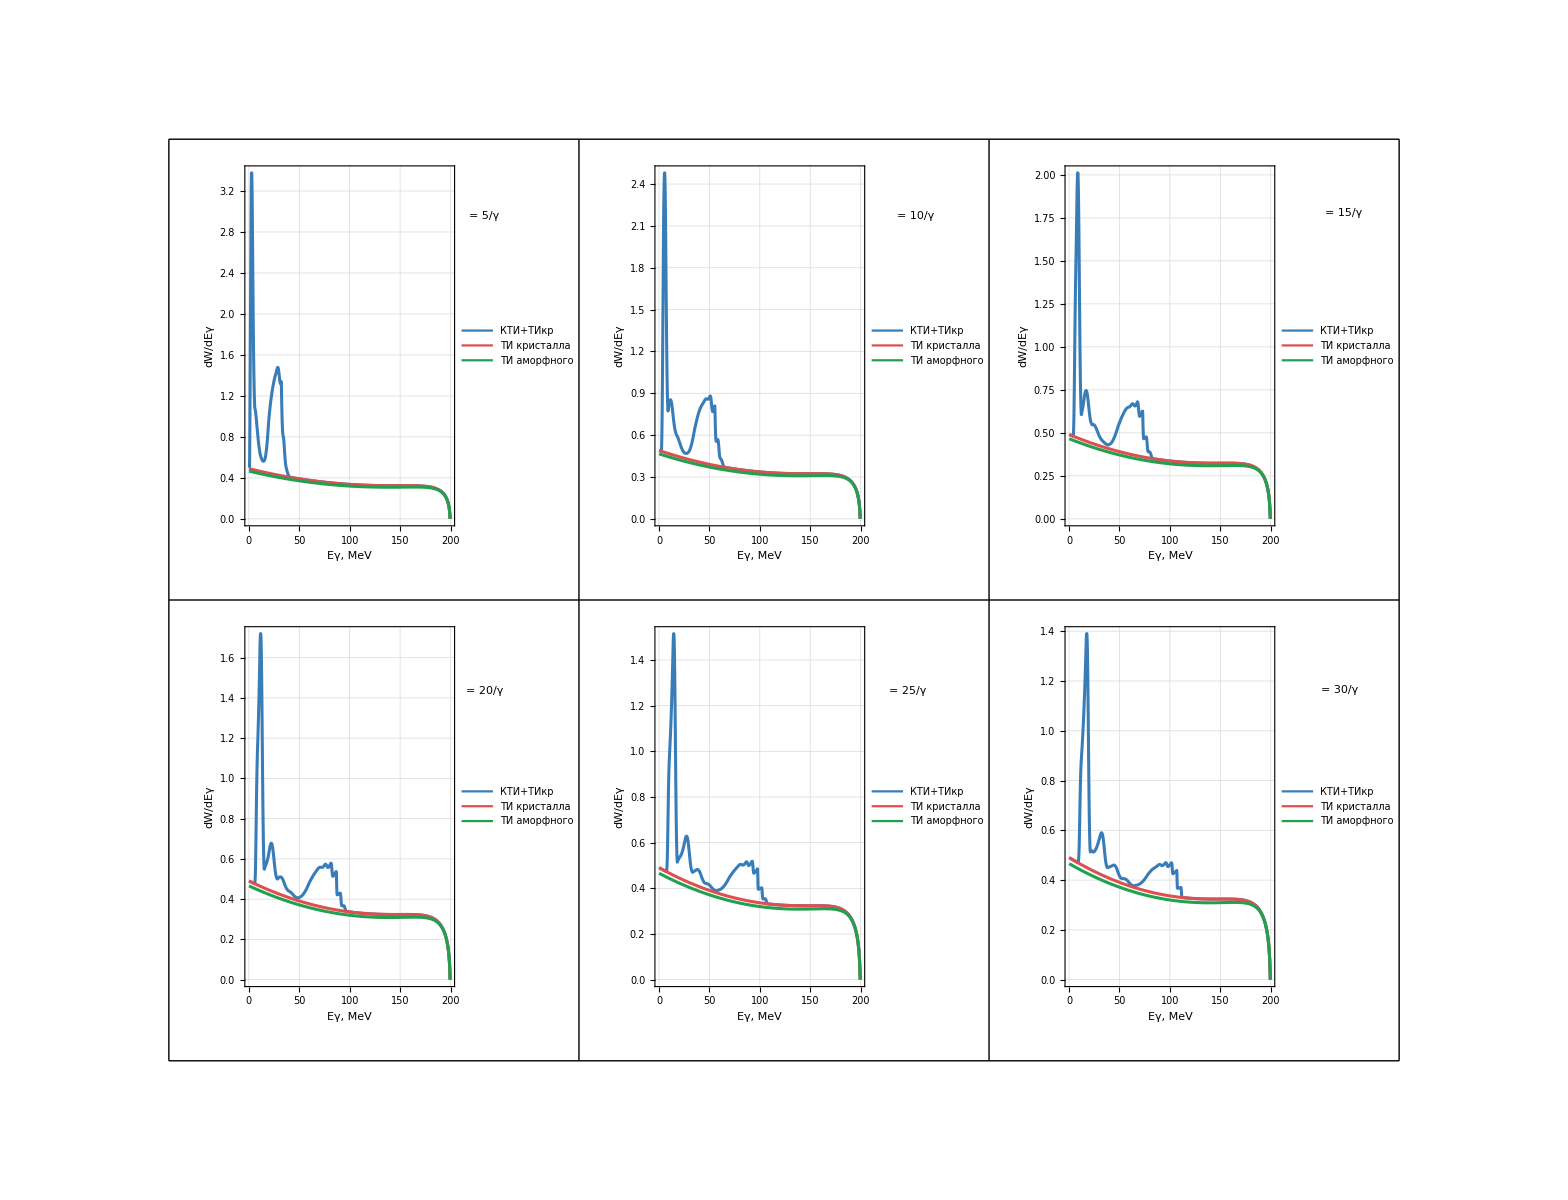

```mathematica
r11=ComputeFile["skif20_5gC.txt",20*10^-6];
r12=ComputeFile["skif20_10gC.txt",20*10^-6];
r13=ComputeFile["skif20_15gC.txt",20*10^-6];
r14=ComputeFile["skif20_20gC.txt",20*10^-6];
r15=ComputeFile["skif20_25gC.txt",20*10^-6];
r16=ComputeFile["skif20_30gC.txt",20*10^-6];
```

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60916} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.61115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
y11=graphY[r11];
y12=graphY[r12];
y13=graphY[r13];
y14=graphY[r14];
y15=graphY[r15];
y16=graphY[r16];
GraphicsGrid[{{y11,y12,y13},{y14,y15,y16}},ImageSize->{2000,1200}, Spacings->{10,10},Frame->All, Alignment->{Center,Top}]
```

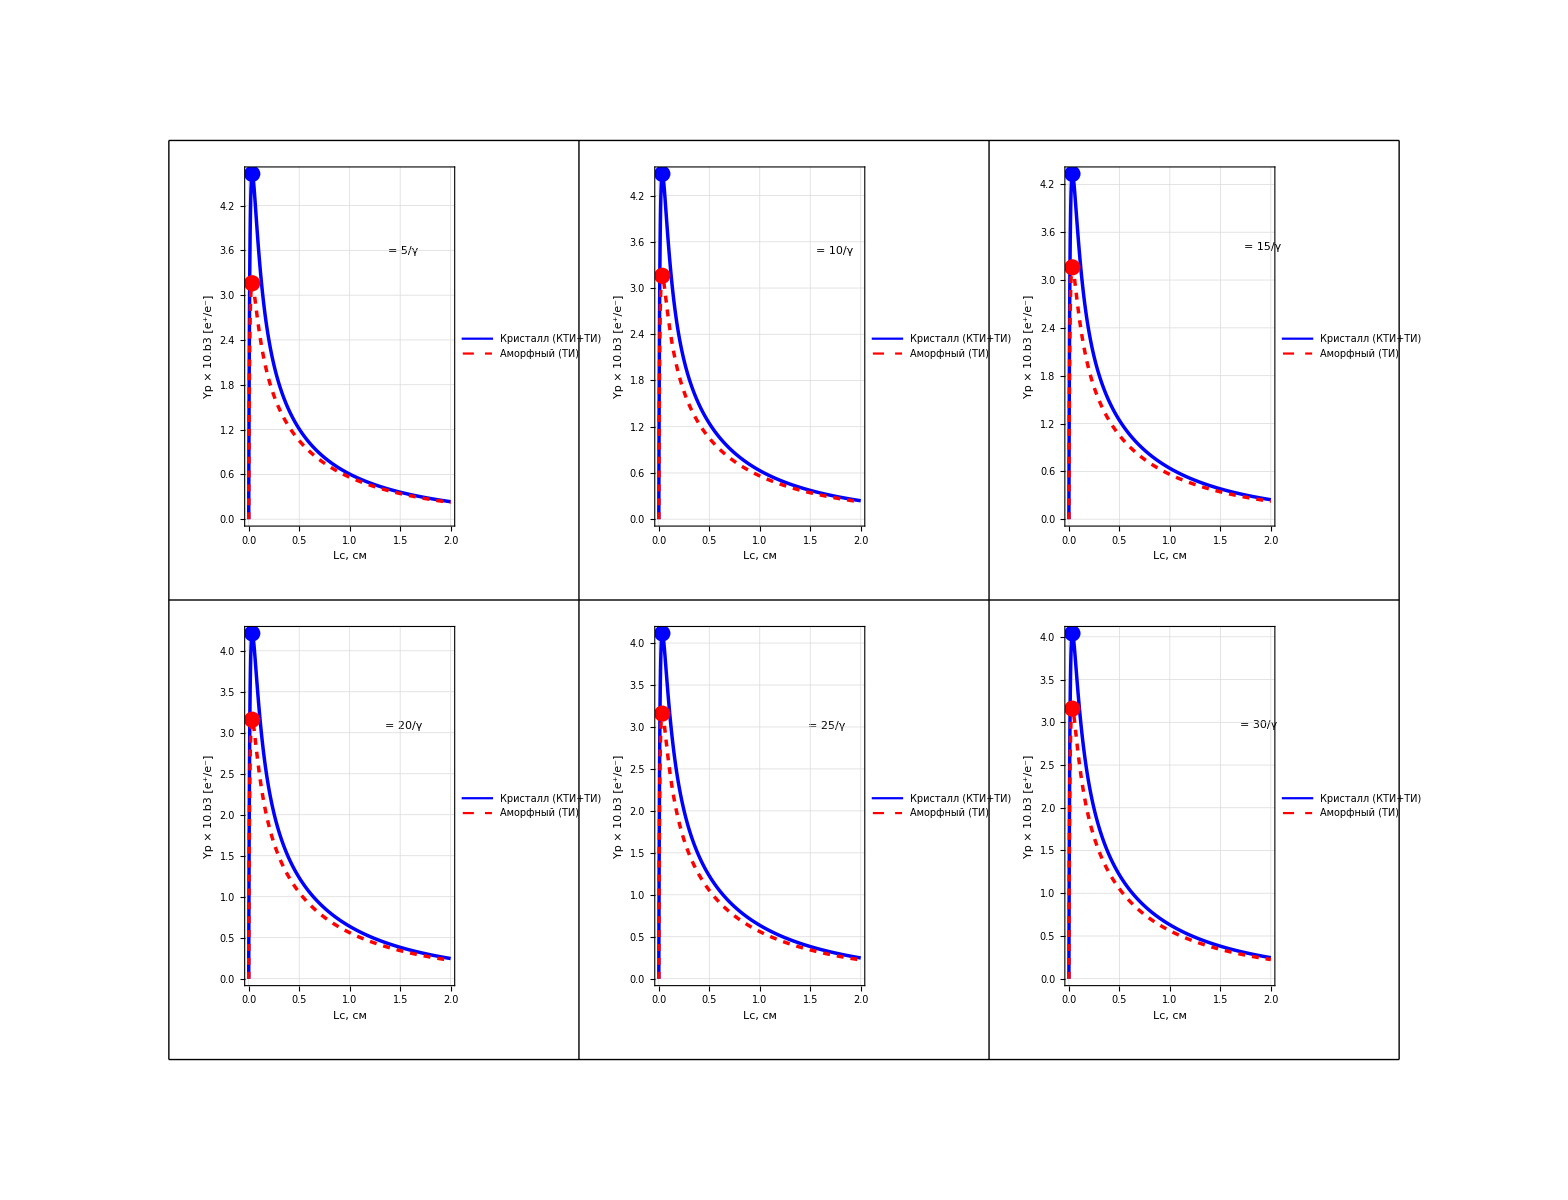

```mathematica
N11=graphN[r11];
N12=graphN[r12];
N13=graphN[r13];
N14=graphN[r14];
N15=graphN[r15];
N16=graphN[r16];
GraphicsGrid[{{N11,N12,N13},{N14,N15,N16}},ImageSize->{2000,1200}, Spacings->{10,10},Frame->All, Alignment->{Center,Top}]
```

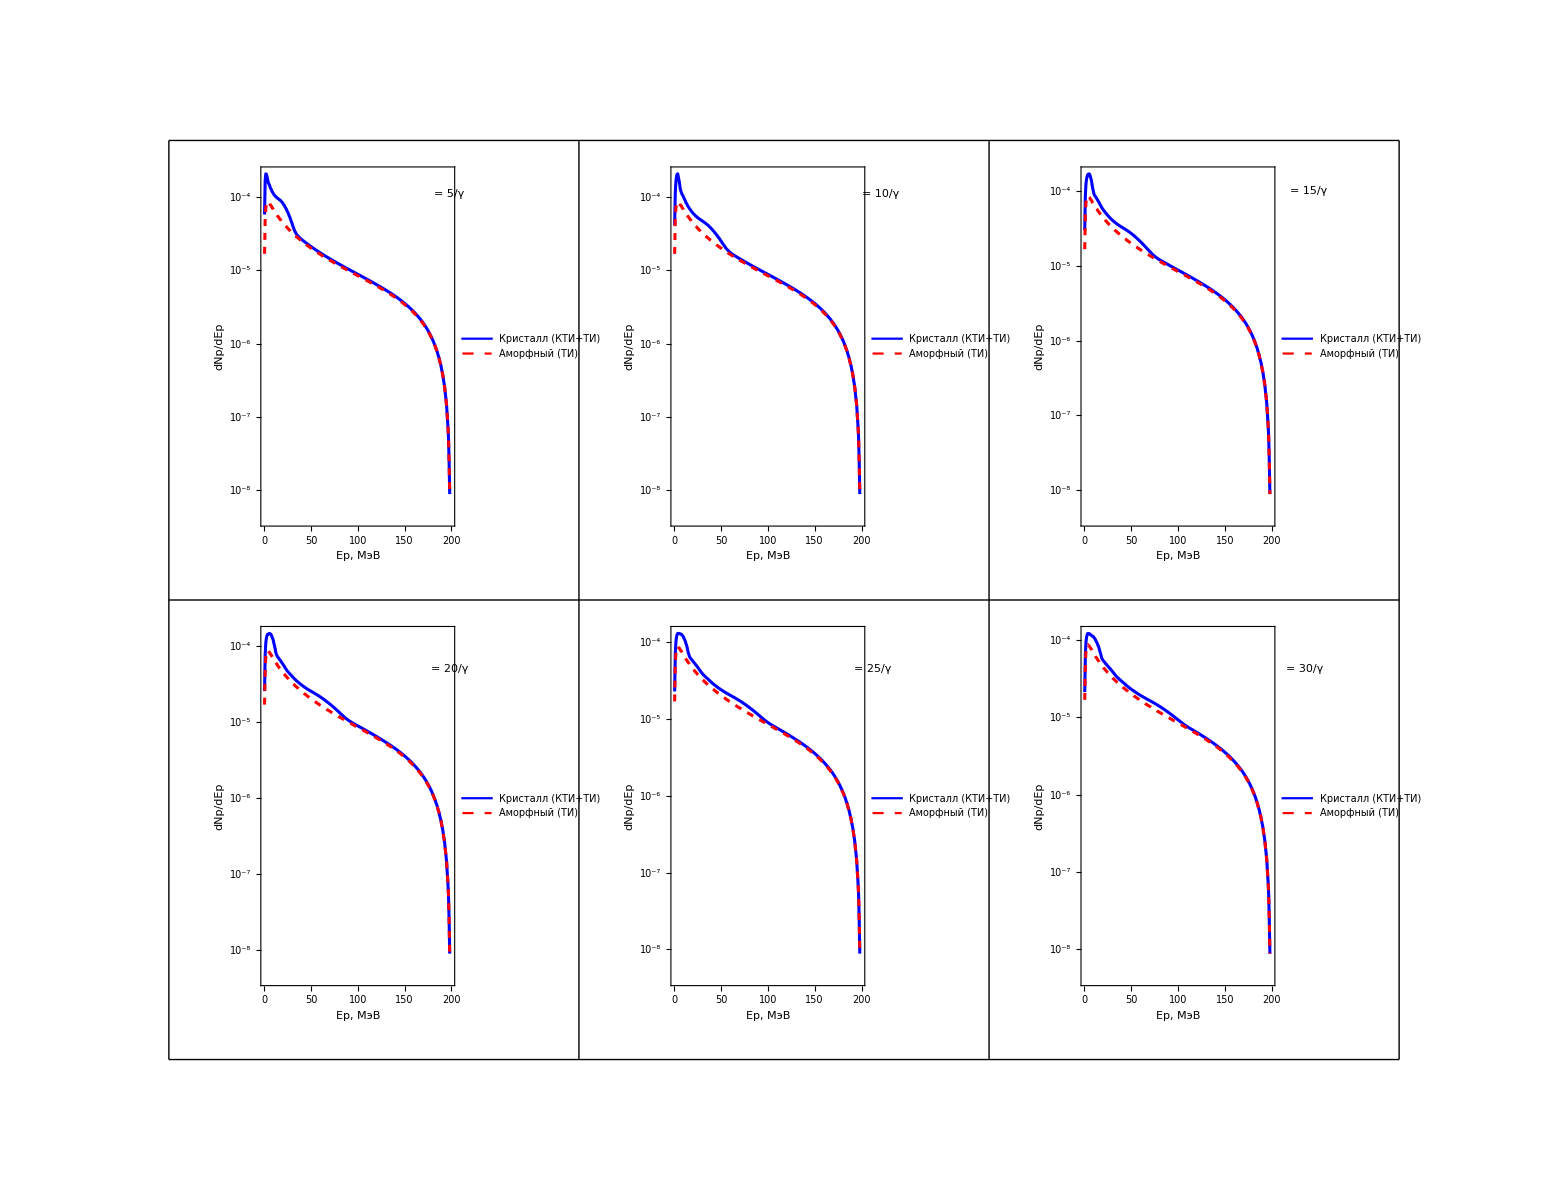

```mathematica
{list11,list12,list13, list14}=LoadSpectrumFile["skif10.txt"];
{list21,list22,list23, list24}=LoadSpectrumFile["skif20.txt"];
{list31,list32,list33, list34}=LoadSpectrumFile["skif30.txt"];
{list61,list62,list63, list64}=LoadSpectrumFile["skif60.txt"];
{list2110g,list2210g,list2310g, list2410g}=LoadSpectrumFile["skif20_10g.txt"];
{list2120g,list2220g,list2320g, list2420g}=LoadSpectrumFile["skif20_20g.txt"];
{list2130g,list2230g,list2330g, list2430g}=LoadSpectrumFile["skif20_30g.txt"];
{list2140g,list2240g,list2340g, list2440g}=LoadSpectrumFile["skif20_40g.txt"];
{list11C,list12C,list13C, list14C}=LoadSpectrumFile["skif20C_2g.txt"];
{list21C,list22C,list23C, list24C}=LoadSpectrumFile["skif20C.txt"];
{list31C,list32C,list33C, list34C}=LoadSpectrumFile["skif20C_02g.txt"];
{list61C,list62C,list63C, list64C}=LoadSpectrumFile["skif20C_05g.txt"];
```

```mathematica
In1=ListLinePlot[{list21,list22,list23},PlotRange->{{-2,202},{0, 3}},AspectRatio->1,Frame->True,FrameStyle->AbsoluteThickness[2],FrameLabel->{" E_γ, MeV","dW/dE_γ","",""},RotateLabel->True,ImageSize->{800,600},LabelStyle->Directive[Black,FontSize->28, FontFamily-> "Times New Roman" ],PlotStyle->{{Thick,ColorData["DarkBands"][0.3]},{Thick,Dashing[Large],ColorData["SouthwestColors"][1]},{Thick,DotDashed,ColorData["LakeColors"][0.2]},{Thick,Dashing[Large],Thick,ColorData["SouthwestColors"][0.2]},{Thick},{Thick,Blue},{Thick,Dashing[Medium],Red},{Thick,Dashing[Medium],Green},{Thick,Black}},Axes->{False,True}];
In2=ListLinePlot[{list21C,list22C,list23C},PlotRange->{{-2,202},{0, 3}},AspectRatio->1,Frame->True,FrameStyle->AbsoluteThickness[2],FrameLabel->{" E_γ, MeV","dW/dE_γ","",""},RotateLabel->True,ImageSize->{800,600},LabelStyle->Directive[Black,FontSize->28, FontFamily-> "Times New Roman" ],PlotStyle->{{Thick,ColorData["DarkBands"][0.3]},{Thick,Dashing[Large],ColorData["SouthwestColors"][1]},{Thick,DotDashed,ColorData["LakeColors"][0.2]},{Thick,Dashing[Large],Thick,ColorData["SouthwestColors"][0.2]},{Thick},{Thick,Blue},{Thick,Dashing[Medium],Red},{Thick,Dashing[Medium],Green},{Thick,Black}},Axes->{False,True}];
In3=ListLinePlot[{list2130g,list2230g,list2330g},PlotRange->{{-2,202},{0, 3}},AspectRatio->1,Frame->True,FrameStyle->AbsoluteThickness[2],FrameLabel->{" E_γ, MeV","dW/dE_γ","",""},RotateLabel->True,ImageSize->{800,600},LabelStyle->Directive[Black,FontSize->28, FontFamily-> "Times New Roman" ],PlotStyle->{{Thick,ColorData["DarkBands"][0.3]},{Thick,Dashing[Large],ColorData["SouthwestColors"][1]},{Thick,DotDashed,ColorData["LakeColors"][0.2]},{Thick,Dashing[Large],Thick,ColorData["SouthwestColors"][0.2]},{Thick},{Thick,Blue},{Thick,Dashing[Medium],Red},{Thick,Dashing[Medium],Green},{Thick,Black}},Axes->{False,True}];
GraphicsGrid[{{In1},{In2},{In3}},ImageSize->{800,1800}, Spacings->{-150,10},Frame->All, Alignment->{Center,Top}]
```

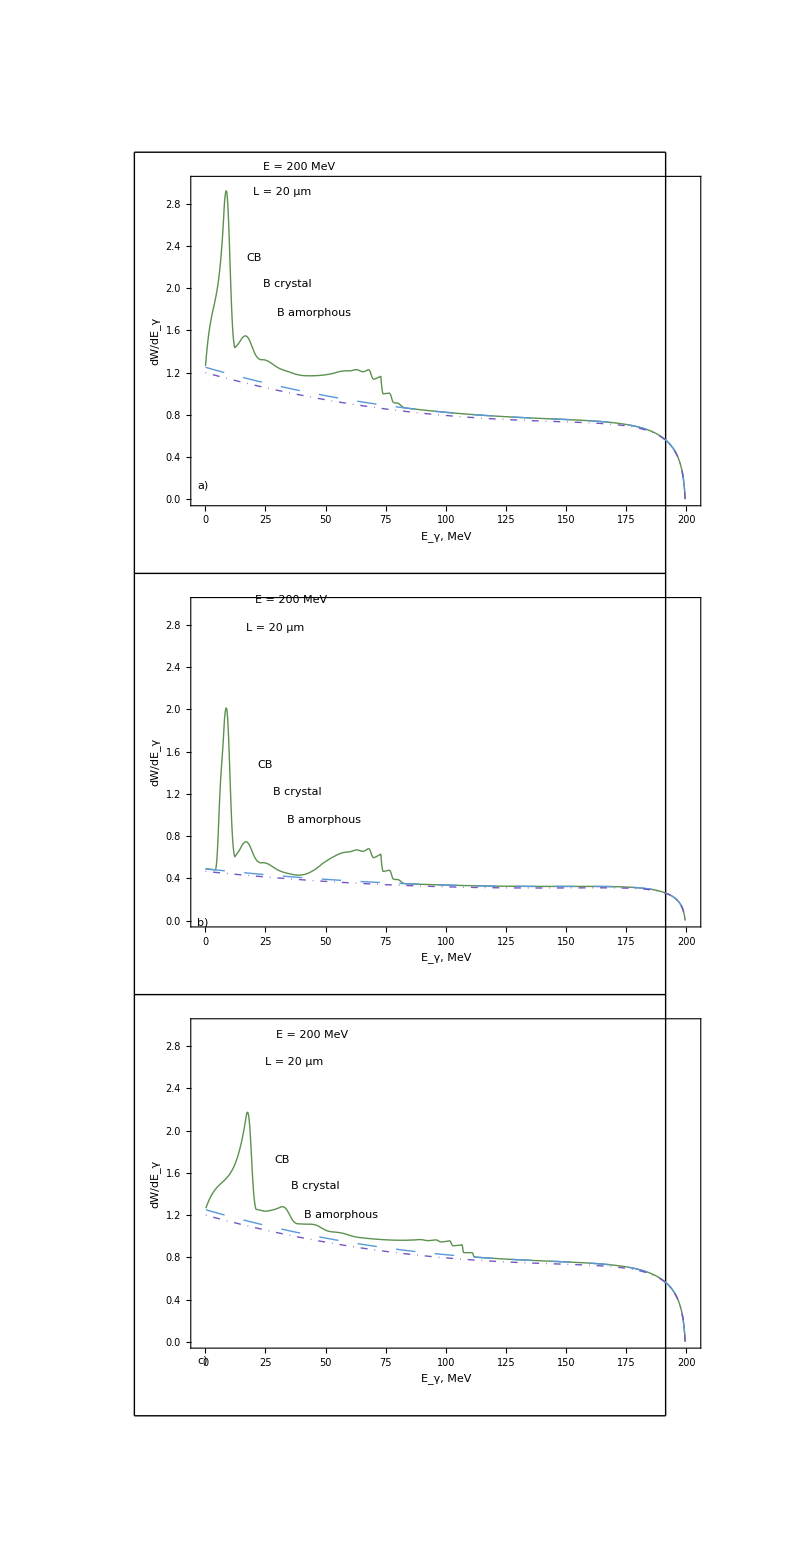

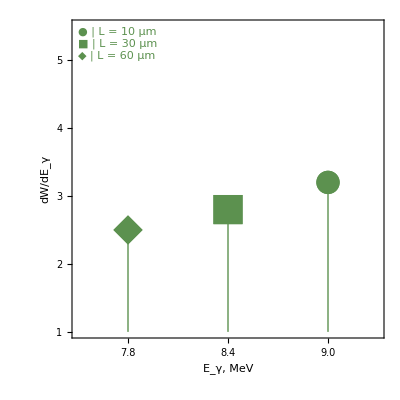

```mathematica
PlotPeakMarkers[list11_,list31_,list61_]:=Module[{x1num,x2num,x3num,y1num,y2num,y3num,xMin,xMax,xTicks},(*Находим пиковые значения и округляем до десятых*){x1num,y1num}=Round[list11[[First[Ordering[list11[[All,2]],-1]]]],0.1];
{x2num,y2num}=Round[list31[[First[Ordering[list31[[All,2]],-1]]]],0.1];
{x3num,y3num}=Round[list61[[First[Ordering[list61[[All,2]],-1]]]],0.1];
xMin=Min[x1num,x2num,x3num]-0.3;
xMax=Max[x1num,x2num,x3num]+0.3;
(*Форматируем подписи с одним знаком после запятой*)xTicks={{x1num,NumberForm[x1num,{Infinity,1}]},{x2num,NumberForm[x2num,{Infinity,1}]},{x3num,NumberForm[x3num,{Infinity,1}]}};
ListPlot[{{{x1num,y1num}},{{x2num,y2num}},{{x3num,y3num}}},PlotStyle->ColorData["DarkBands"][0.3],PlotMarkers->{Style["●",24],Style["■",30],Style["◆",30]},PlotRange->{{xMin,xMax},{1,5.5}},Frame->True,FrameLabel->{"\!\(\*SubscriptBox[\(E\), \(γ\)]\), MeV","dW/\!\(\*SubscriptBox[\(dE\), \(γ\)]\)"},FrameTicks->{{Range[1,5],None},{xTicks,None}},LabelStyle->Directive[Black,FontSize->28,FontFamily->"Times New Roman"],PlotRangeClipping->False,ImagePadding->{{80,20},{80,20}},Epilog->{ColorData["DarkBands"][0.3],Thick,Line[{{x1num,1},{x1num,y1num}}],Line[{{x2num,1},{x2num,y2num}}],Line[{{x3num,1},{x3num,y3num}}],(*Легенда*)Inset[Grid[{{Style["●",24,ColorData["DarkBands"][0.3]],Style["L = 10 μm",FontSize->20,FontFamily->"Times New Roman",Black]},{Style["■",30,ColorData["DarkBands"][0.3]],Style["L = 30 μm",FontSize->20,FontFamily->"Times New Roman",Black]},{Style["◆",30,ColorData["DarkBands"][0.3]],Style["L = 60 μm",FontSize->20,FontFamily->"Times New Roman",Black]}},Alignment->Left,Spacings->{1,1}],Scaled[{0.02,0.98}],{Left,Top},Background->White]},AspectRatio->1,ImageSize->400]]

PlotPeakMarkers[list11,list31,list61]
```

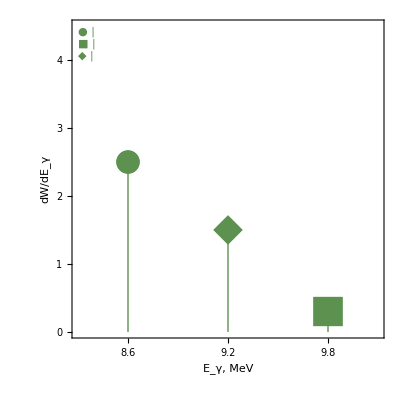

```mathematica
PlotPeakMarkers[list11_,list31_,list61_]:=Module[{x1num,x2num,x3num,y1num,y2num,y3num,xMin,xMax,xTicks},(*Находим пиковые значения и округляем до десятых*){x1num,y1num}=Round[list11[[First[Ordering[list11[[All,2]],-1]]]],0.1];
{x2num,y2num}=Round[list31[[First[Ordering[list31[[All,2]],-1]]]],0.1];
{x3num,y3num}=Round[list61[[First[Ordering[list61[[All,2]],-1]]]],0.1];
xMin=Min[x1num,x2num,x3num]-0.3;
xMax=Max[x1num,x2num,x3num]+0.3;
(*Форматируем подписи с одним знаком после запятой*)xTicks={{x1num,NumberForm[x1num,{Infinity,1}]},{x2num,NumberForm[x2num,{Infinity,1}]},{x3num,NumberForm[x3num,{Infinity,1}]}};
ListPlot[{{{x1num,y1num}},{{x2num,y2num}},{{x3num,y3num}}},PlotStyle->ColorData["DarkBands"][0.3],PlotMarkers->{Style["●",24],Style["■",30],Style["◆",30]},PlotRange->{{xMin,xMax},{0,4.5}},Frame->True,FrameLabel->{"\!\(\*SubscriptBox[\(E\), \(γ\)]\), MeV","dW/\!\(\*SubscriptBox[\(dE\), \(γ\)]\)"},FrameTicks->{{Range[0,4],None},{xTicks,None}},LabelStyle->Directive[Black,FontSize->28,FontFamily->"Times New Roman"],PlotRangeClipping->False,ImagePadding->{{80,20},{80,20}},Epilog->{ColorData["DarkBands"][0.3],Thick,Line[{{x1num,0},{x1num,y1num}}],Line[{{x2num,0},{x2num,y2num}}],Line[{{x3num,0},{x3num,y3num}}],(*Легенда*)Inset[Grid[{{Style["●",24,ColorData["DarkBands"][0.3]],Style["",FontSize->20,FontFamily->"Times New Roman",Black]},{Style["■",30,ColorData["DarkBands"][0.3]],Style["",FontSize->20,FontFamily->"Times New Roman",Black]},{Style["◆",30,ColorData["DarkBands"][0.3]],Style["",FontSize->20,FontFamily->"Times New Roman",Black]}},Alignment->Left,Spacings->{1,1}],Scaled[{0.02,0.98}],{Left,Top},Background->White]},AspectRatio->1,ImageSize->400]]
PlotPeakMarkers[list11C,list31C,list61C]
```

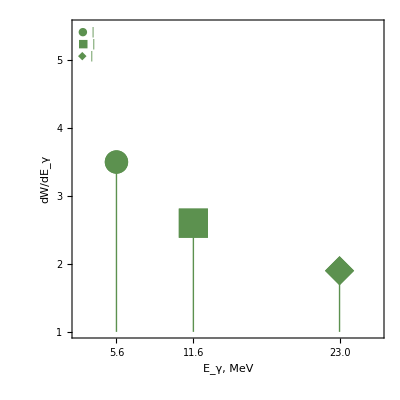

```mathematica
PlotPeakMarkers[list11_,list31_,list61_]:=Module[{x1num,x2num,x3num,y1num,y2num,y3num,xMin,xMax,xTicks},(*Находим пиковые значения и округляем до десятых*){x1num,y1num}=Round[list11[[First[Ordering[list11[[All,2]],-1]]]],0.1];
{x2num,y2num}=Round[list31[[First[Ordering[list31[[All,2]],-1]]]],0.1];
{x3num,y3num}=Round[list61[[First[Ordering[list61[[All,2]],-1]]]],0.1];
xMin=Min[x1num,x2num,x3num]-3;
xMax=Max[x1num,x2num,x3num]+3;
(*Форматируем подписи с одним знаком после запятой*)xTicks={{x1num,NumberForm[x1num,{Infinity,1}]},{x2num,NumberForm[x2num,{Infinity,1}]},{x3num,NumberForm[x3num,{Infinity,1}]}};
ListPlot[{{{x1num,y1num}},{{x2num,y2num}},{{x3num,y3num}}},PlotStyle->ColorData["DarkBands"][0.3],PlotMarkers->{Style["●",24],Style["■",30],Style["◆",30]},PlotRange->{{xMin,xMax},{1,5.5}},Frame->True,FrameLabel->{"\!\(\*SubscriptBox[\(E\), \(γ\)]\), MeV","dW/\!\(\*SubscriptBox[\(dE\), \(γ\)]\)"},FrameTicks->{{Range[1,5],None},{xTicks,None}},LabelStyle->Directive[Black,FontSize->28,FontFamily->"Times New Roman"],PlotRangeClipping->False,ImagePadding->{{80,20},{80,20}},Epilog->{ColorData["DarkBands"][0.3],Thick,Line[{{x1num,1},{x1num,y1num}}],Line[{{x2num,1},{x2num,y2num}}],Line[{{x3num,1},{x3num,y3num}}],(*Легенда*)Inset[Grid[{{Style["●",24,ColorData["DarkBands"][0.3]],Style["",FontSize->20,FontFamily->"Times New Roman",Black]},{Style["■",30,ColorData["DarkBands"][0.3]],Style["",FontSize->20,FontFamily->"Times New Roman",Black]},{Style["◆",30,ColorData["DarkBands"][0.3]],Style["",FontSize->20,FontFamily->"Times New Roman",Black]}},Alignment->Left,Spacings->{1,1}],Scaled[{0.02,0.98}],{Left,Top},Background->White]},AspectRatio->1,ImageSize->400]]
PlotPeakMarkers[list2110g,list2120g,list2140g]
```

```mathematica
Text[Style["L = 20 μm",28,FontFamily->"Times New Roman"]]
```

L = 20 μm

```mathematica
Text[Row[{Graphics[{Thick,Dashing[Medium],ColorData["SouthwestColors"][1],Line[{{0,60},{30,60}}]},ImageSize->{30,40},AspectRatio->1], Style[" B amorphous",28,FontFamily->"Times New Roman"]}]]
```

-Graphics- B amorphous

```mathematica
r11=ComputeFile["skif20.txt",20*10^-6];
r12=ComputeFile["skif20_500M.txt",20*10^-6];
r13=ComputeFile["skif20_800M.txt",20*10^-6];
r14=ComputeFile["skif20_1600M.txt",20*10^-6];
r12C=ComputeFile["skif20C.txt",20*10^-6];
```

InterpolatingFunction::dmval: Input value {4.60557} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60597} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60637} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.61016} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {Log[101]} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.62006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.61314} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.62104} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.62889} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.61314} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.62889} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {Log[104]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.60557} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60597} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60637} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
y12=graphY[r11];
y12C=graphY[r12C];
N12=graphN[r11];
GraphicsGrid[{{y12},{y12C}, {N12}},ImageSize->{800,1800}, Spacings->{-150,10},Frame->All, Alignment->{Center,Top}]
```

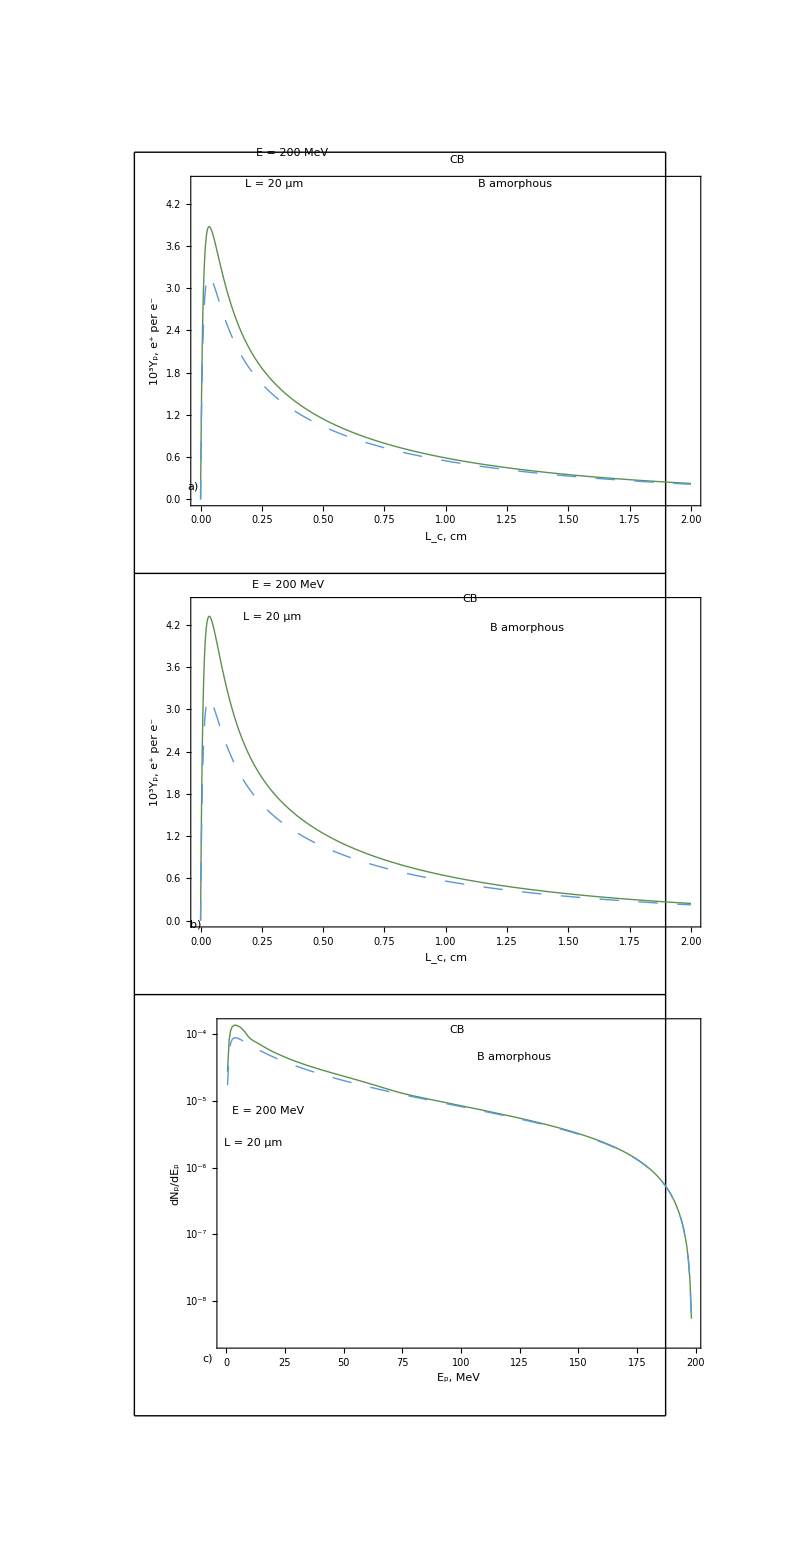

```mathematica
{Xpeak,Ypeak}=list2110g[[First[Ordering[list2110g[[All,2]],-1]]]]
```

{5.6,3.48443}

```mathematica
peakX={r11["niMax"]*ΔL,r11["niMaxA"]*ΔL}
peakY={1000*r11C["Yp"][[r11C["niMax"]]],1000*r16["YpA"][[r16["niMaxA"]]]}
```

{0.035,0.034}

{2.16229,9.53512}

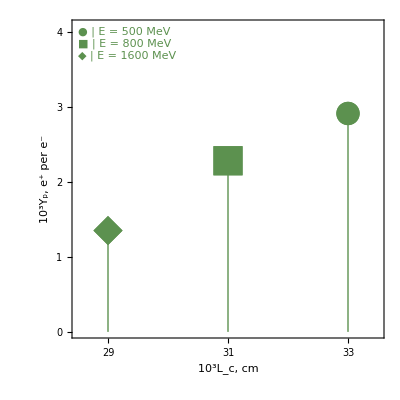

```mathematica
PlotPeakMarkersYp[r1_,r2_,r3_,labels_]:=Module[{x1,y1,x2,y2,x3,y3,xMin,xMax,xTicks},{x1,y1}=Round[{1000*r1["niMax"]*ΔL,1000*r1["Yp"][[r1["niMax"]]]},0.01];
{x2,y2}=Round[{r2["niMax"]*ΔL*1000,1000*r2["Yp"][[r2["niMax"]]]},0.01];
{x3,y3}=Round[{r3["niMax"]*ΔL*1000,1000*r3["Yp"][[r3["niMax"]]]},0.01];
xMin=Min[x1,x2,x3]-0.5;
xMax=Max[x1,x2,x3]+0.5;
xTicks={{x1,ToString[Round[x1]]},{x2,ToString[Round[x2]]},{x3,ToString[Round[x3]]}};
ListPlot[{{{x1,y1}},{{x2,y2}},{{x3,y3}}},PlotStyle->ColorData["DarkBands"][0.3],PlotMarkers->{Style["●",24],Style["■",30],Style["◆",30]},PlotRange->{{xMin,xMax},{0,1.4*Max[y1,y2,y3]}},Frame->True,FrameLabel->{"10^3\!\(\*SubscriptBox[\(L\), \(c\)]\), cm","\!\(\*SuperscriptBox[\(10\), \(3\)]\)\!\(\*SubscriptBox[\(Y\), \(p\)]\), \!\(\*SuperscriptBox[\(e\), \(+\)]\) per \!\(\*SuperscriptBox[\(e\), \(-\)]\)"},FrameTicks->{{Table[{i,ToString[i]},{i,0,Ceiling[1.5*Max[y1,y2,y3]]}],None},{xTicks,None}},LabelStyle->Directive[Black,FontSize->28,FontFamily->"Times New Roman"],PlotRangeClipping->False,ImagePadding->{{80,20},{80,20}},Epilog->{ColorData["DarkBands"][0.3],Thick,Line[{{x1,0},{x1,y1}}],Line[{{x2,0},{x2,y2}}],Line[{{x3,0},{x3,y3}}],Inset[Grid[{{Style["●",24,ColorData["DarkBands"][0.3]],Style[labels[[1]],FontSize->20,FontFamily->"Times New Roman",Black]},{Style["■",30,ColorData["DarkBands"][0.3]],Style[labels[[2]],FontSize->20,FontFamily->"Times New Roman",Black]},{Style["◆",30,ColorData["DarkBands"][0.3]],Style[labels[[3]],FontSize->20,FontFamily->"Times New Roman",Black]}},Alignment->Left,Spacings->{1,1}],Scaled[{0.02,0.98}],{Left,Top},Background->White]},AspectRatio->1,ImageSize->400]]
PlotPeakMarkersYp[r12,r13,r14,{"E = 500 MeV","E = 800 MeV","E = 1600 MeV"}]
```

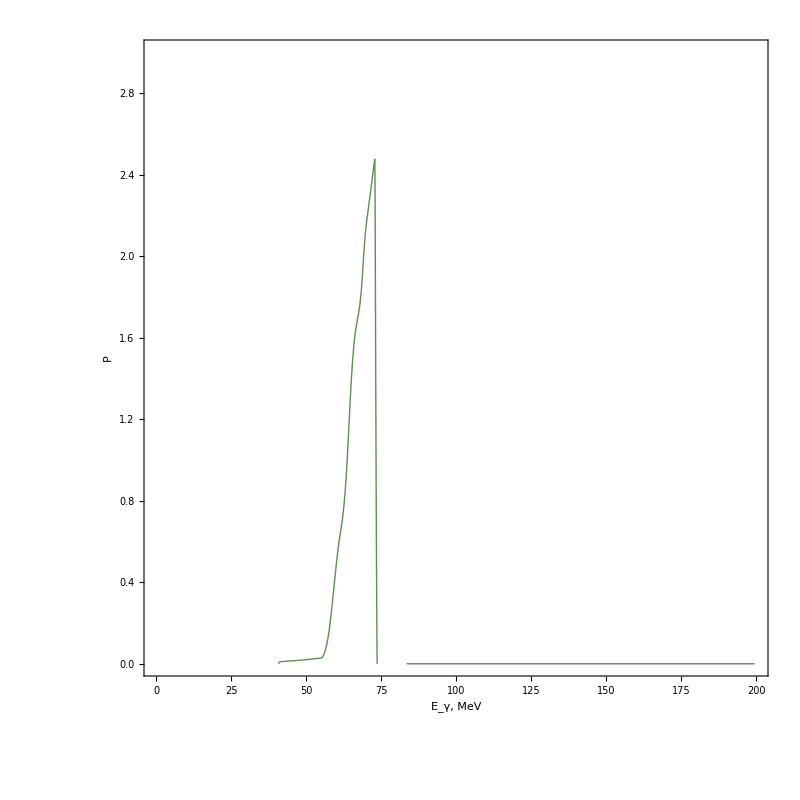

```mathematica
graphPol["skif20.txt"]
```

InterpolatingFunction::dmval: Input value {4.60557} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60597} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60637} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

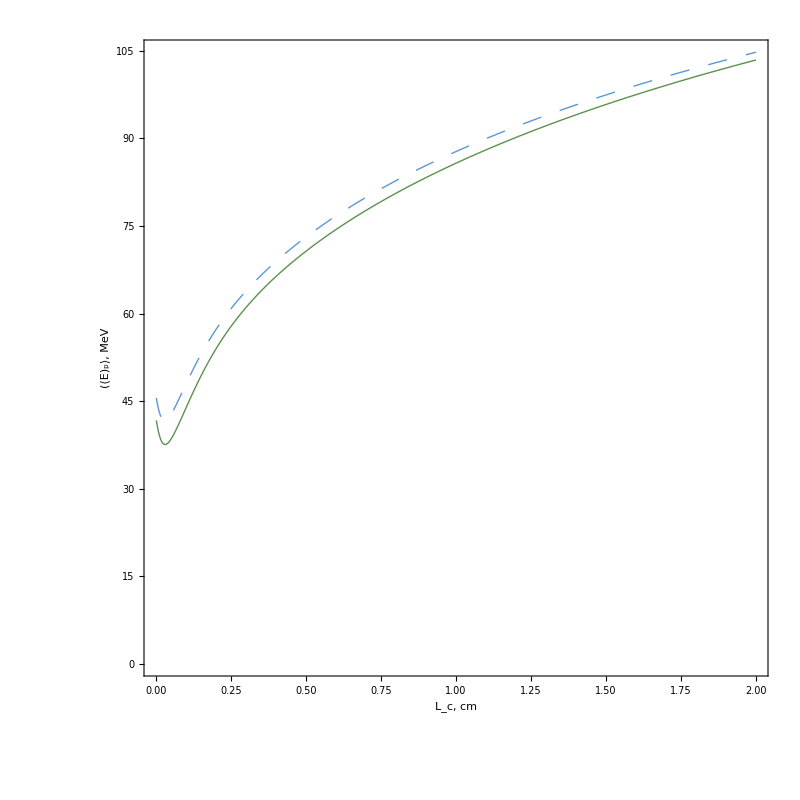

InterpolatingFunction::dmval: Input value {4.60557} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60597} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60637} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

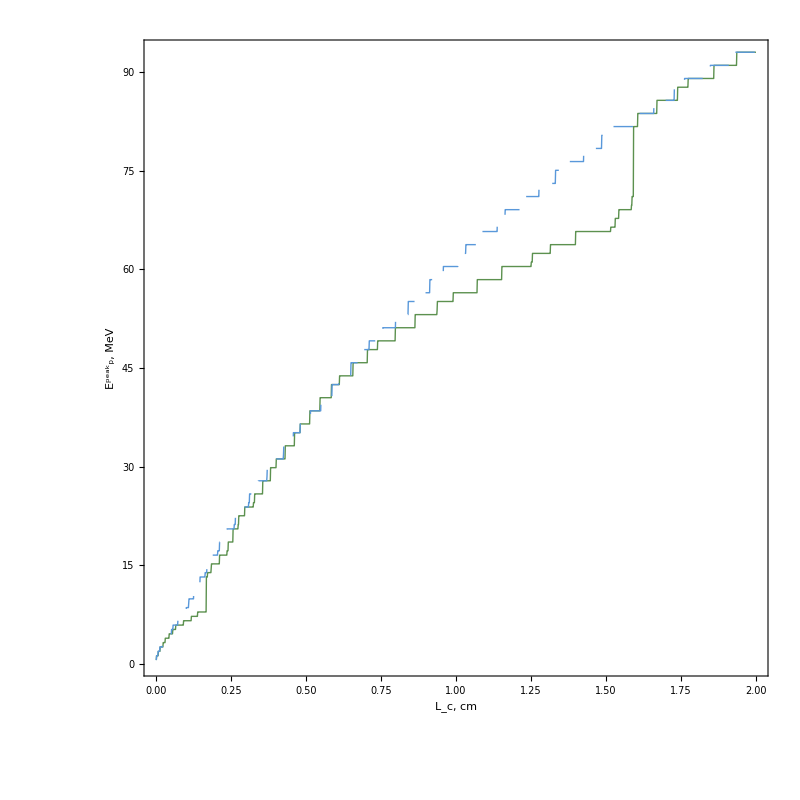

```mathematica
graphMeanEp["skif20.txt"]
graphPeakEp["skif20.txt"]
```

```mathematica
r11=ComputeFile["skif20.txt",20*10^-6];
```

InterpolatingFunction::dmval: Input value {4.60557} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60597} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.60637} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

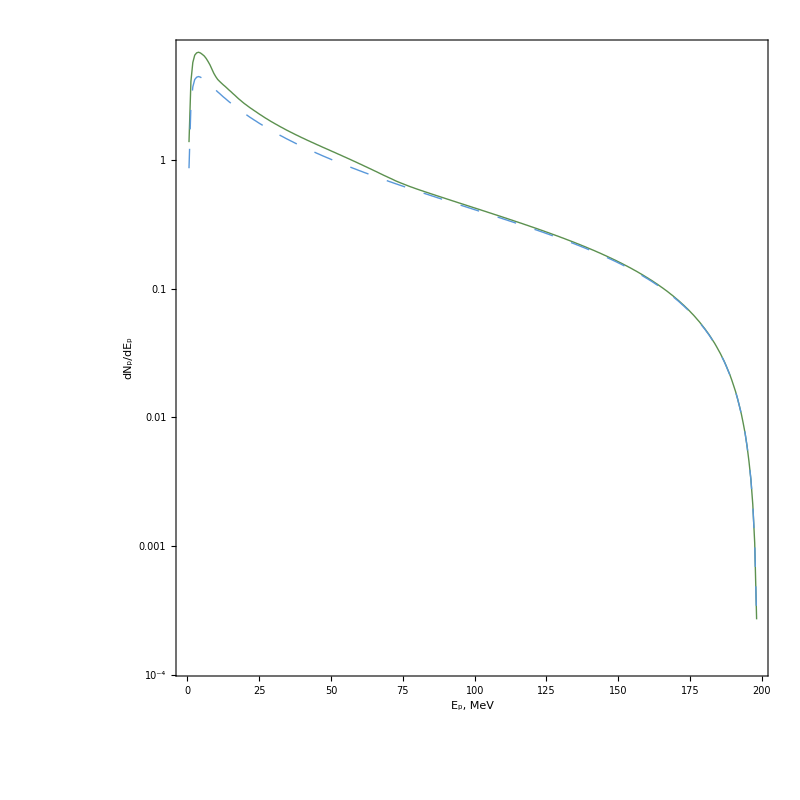

```mathematica
N12=graphN[r11]
```

```mathematica
NEpPts=300;
EpMin=0.01;  (*почти от нуля*)
EpMax=En0-me;
EpGrid=N@Table[EpMin+(EpMax-EpMin)*(j-1)/(NEpPts-1),{j,1,NEpPts}];
```

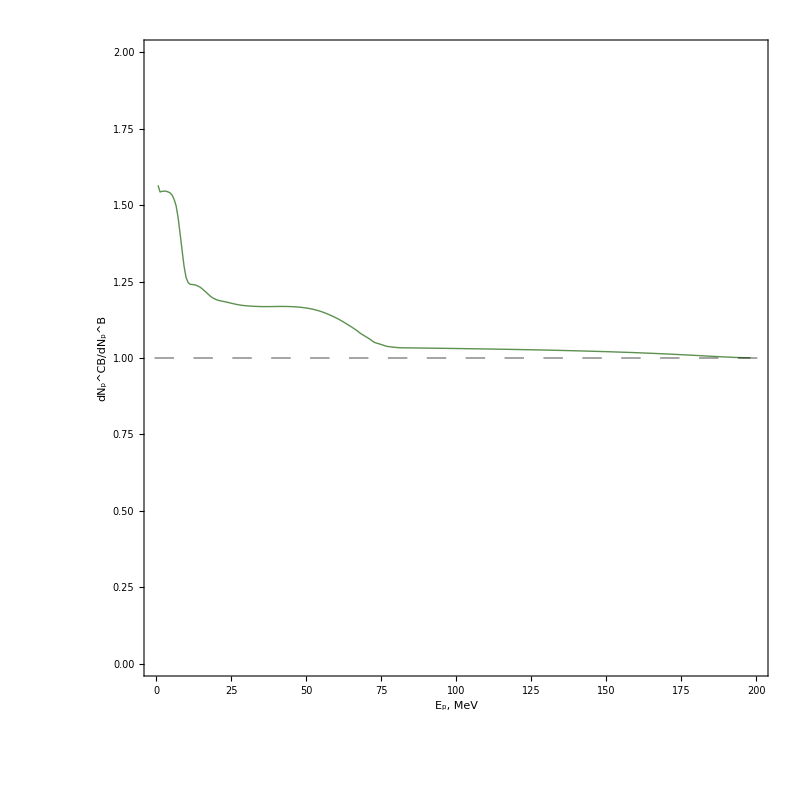

```mathematica
graphNRatio[r_]:=Module[{niMaxG,niMaxA,specG,specA,ratioData},niMaxG=r["niMax"];
niMaxA=r["niMaxA"];
specG=r["spec"][[niMaxG]];
specA=r["specA"][[niMaxA]];
ratioData=Table[If[specA[[i]]>1*^-10&&specG[[i]]>1*^-10,{EpGrid[[i]],specG[[i]]/specA[[i]]},Nothing],{i,1,Length[EpGrid]}];
ListLinePlot[ratioData,AspectRatio->1,Frame->True,FrameStyle->AbsoluteThickness[2],FrameLabel->{" \!\(\*SubscriptBox[\(E\), \(p\)]\), MeV","\!\(\*SubsuperscriptBox[\(dN\), \(p\), \(CB\)]\)/\!\(\*SubsuperscriptBox[\(dN\), \(p\), \(Β\)]\)","",""},RotateLabel->True,ImageSize->{800,600},LabelStyle->Directive[Black,FontSize->28,FontFamily->"Times New Roman"],PlotStyle->{{Thick,ColorData["DarkBands"][0.3]}},Axes->{False,True},PlotRange->{{0,200},{0,2}},GridLines->{{},{1}},GridLinesStyle->Directive[Black,Dashing[Large],Thick]]];
graphNRatio[r11]
```

```mathematica
Table[{EpGrid[[i]],r11["spec"][[35]][[i]],r11["specA"][[34]][[i]],r11["spec"][[35]][[i]]/r11["specA"][[34]][[i]]},{i,1,10}]//TableForm
```

0.561 | 1.37119 | 0.860416 | 1.59364
1.22631 | 4.06117 | 2.63111 | 1.54352
1.89162 | 5.69667 | 3.68715 | 1.54501
2.55693 | 6.4921 | 4.19969 | 1.54585
3.22224 | 6.7666 | 4.37823 | 1.54551
3.88756 | 6.84297 | 4.43128 | 1.54424
4.55287 | 6.75082 | 4.38095 | 1.54095
5.21818 | 6.58229 | 4.28984 | 1.53439
5.88349 | 6.39379 | 4.19539 | 1.524
6.5488 | 6.11855 | 4.07073 | 1.50306